## ModelSWITCH

```mathematica
(* =============================================================== *)
(* Poisson switching + dynamic encounters at BOTH legs.            *)
(* PDF of loop length x=L/lp, independently normalized by state.    *)
(* beta = tau/tsw. Fits original nine-state balance model.          *)
(* =============================================================== *)

ClearAll[
  x, gb, gc, h, α, β, A1, Ab1, Ac1, Abp, Acp,
  Abb, Abc, Acb, Acc,
  gammaBare, gb0, alpha0,
  switchData, switchRaw, switchNorm, switchWeight, switchExpCoeffs,
  AF, Anorm, A11norm, Abnorm, AbbNorm, A00norm,
  Ab1norm, Ac1norm, Abpnorm, Acpnorm, Abcnorm, Acbnorm, Accnorm,
  AbAnynorm
];

gammaBare = 2.7;    (* BARE cohesin density; NOT gc *)
gb0 = 4;
alpha0 = 1.2;

(* Always pass the current base parameters as explicit cache keys. *)
switchData[be_?NumericQ] := switchData[be, gammaBare, gb0, alpha0];

switchData[be_?NumericQ, gm_?NumericQ, gbv_?NumericQ,
   al_?NumericQ] /; be >= 0 && gm > 0 && gbv >= 0 && al >= 0 :=
 switchData[be, gm, gbv, al] = Module[
   {aB, pB, pFree, z, jj, j0, p0, h0, gc0, pars,
    moving, blocked, rhs, algebraic, mm, mb, bm, bb,
    sb, mat, e0, intMoving, stateNames, stateRows,
    rows, weights, lambda, eigenvectors, modes, coeffs,
    nm, k},

   (* Self-consistent moving fraction, using the 4 marginal balances. *)
   aB = gbv*(1 + al + be)/((1 + al)*(1 + al + 2*be));
   pB = gbv*be/((1 + al)*(1 + al + 2*be));
   pFree[z_] := (2 + z*(be*(1 + aB) - (2 + be)*pB))/
     (2 + be + gm*z/2);

   j0 = jj /. FindRoot[
       (gm + gm*jj/2)*jj - (2 + be)*(1 - (1 + aB)*jj) +
         be*(1 - pB*jj - pFree[jj]) == 0,
       {jj, 0.35, 0.0, 1.0}];
   p0 = pFree[j0];
   h0 = gm*j0/2;
   gc0 = gm + h0;
   pars = {gb -> gbv, gc -> gc0, h -> h0,
     α -> al, β -> be};

   (* Moving:  A1, Ab1, Ac1.
      Blocked: Abp, Acp, Abb, Abc, Acb, Acc. *)
   moving = {A1[x], Ab1[x], Ac1[x]};
   blocked = {Abp[x], Acp[x], Abb[x], Abc[x], Acb[x], Acc[x]};

   rhs = {
     -(1 + gb + gc + h)*A1[x] +
       α*(Abp[x] + Ab1[x]) + Acp[x] + Ac1[x],
     -(1 + gb + gc + β + α)*Ab1[x] +
       α*Abb[x] + Acb[x] + β*Abp[x],
     h*A1[x] - (2 + gb + gc + β)*Ac1[x] +
       α*Abc[x] + Acc[x] + β*Acp[x]
   };

   algebraic = {
     gb*A1[x] + α*Abb[x] + Abc[x] + β*Ab1[x] -
       (1 + α + β + h)*Abp[x],
     gc*A1[x] + α*Acb[x] + Acc[x] + β*Ac1[x] -
       (2 + β + h)*Acp[x],
     gb*Ab1[x] - (1 + 2*α)*Abb[x],
     gb*Ac1[x] + h*Abp[x] + β*Acb[x] -
       (2 + α + β)*Abc[x],
     gc*Ab1[x] + β*Abc[x] -
       (2 + α + β)*Acb[x],
     gc*Ac1[x] + h*Acp[x] - 3*Acc[x]
   };

   mm = N[Table[Coefficient[Expand[rhs[[i]]], moving[[j]]],
       {i, 3}, {j, 3}] /. pars];
   mb = N[Table[Coefficient[Expand[rhs[[i]]], blocked[[j]]],
       {i, 3}, {j, 6}] /. pars];
   bm = N[Table[Coefficient[Expand[algebraic[[i]]], moving[[j]]],
       {i, 6}, {j, 3}] /. pars];
   bb = N[Table[Coefficient[Expand[algebraic[[i]]], blocked[[j]]],
       {i, 6}, {j, 6}] /. pars];

   sb = -LinearSolve[bb, bm];
   mat = Chop[mm + mb.sb];
   e0 = {1., 0., 0.};
   intMoving = LinearSolve[-mat, e0];

   (* Nine state row-vectors on the reduced 3-component solution. *)
   stateNames = {"A11", "Ab1", "Ac1", "Abp", "Acp",
     "Abb", "Abc", "Acb", "Acc"};
   stateRows = AssociationThread[stateNames,
     Join[IdentityMatrix[3], sb]];

   rows = Join[stateRows, <|
       "A" -> Total[Values[stateRows]],
       "Ab" -> stateRows["Ab1"] + stateRows["Abp"],
       "A00" -> stateRows["A11"] + stateRows["Ac1"] +
         stateRows["Acp"] + stateRows["Acc"],
       "AbAny" -> stateRows["Ab1"] + stateRows["Abp"] +
         stateRows["Abc"] + stateRows["Acb"]
     |>];
   (* Abb already exists as one of the nine state rows.
      A = A00 + AbAny + Abb, but A != A00 + Ab + Abb. *)

   weights = AssociationMap[Chop[rows[#].intMoving] &, Keys[rows]];

   {lambda, eigenvectors} = Eigensystem[mat];
   modes = LinearSolve[Transpose[eigenvectors], e0];
   coeffs = AssociationMap[
     Function[name,
       Table[Chop[modes[[k]]*(rows[name].eigenvectors[[k]])],
         {k, 3}]], Keys[rows]];

   <|
     "Beta" -> be, "J" -> j0, "P" -> p0, "h" -> h0,
     "gcActive" -> gc0, "M" -> mat, "Sblocks" -> sb,
     "Rows" -> rows, "Weights" -> weights,
     "Eigenvalues" -> lambda, "Coefficients" -> coeffs,
     "MovingIntegrals" -> intMoving
   |>
 ];

(* Results are explicit sums of three exponentials in the symbolic x. *)
switchRaw[name_String, xArg_, be_?NumericQ] := Module[
  {data = switchData[be]},
  If[!AssociationQ[data] || !KeyExistsQ[data["Coefficients"], name],
    Return[$Failed]];
  Total[data["Coefficients"][name]*Exp[data["Eigenvalues"]*xArg]]
];

switchWeight[name_String, be_?NumericQ] :=
  switchData[be]["Weights"][name];

switchNorm[name_String, xArg_, be_?NumericQ] := Module[
  {weight = switchWeight[name, be]},
  If[!NumericQ[weight] || weight <= 10^-12,
    Return[Indeterminate]];
  switchRaw[name, xArg, be]/weight
];

switchExpCoeffs[name_String, be_?NumericQ] := Module[
  {d = switchData[be], w},
  w = d["Weights"][name];
  If[!NumericQ[w] || w <= 10^-12, Return[Indeterminate]];
  Transpose[{d["Eigenvalues"], d["Coefficients"][name]/w}]
];

(* Functions of TWO arguments: x and beta. *)
AF[xArg_, be_?NumericQ] := switchRaw["A", xArg, be];
Anorm[xArg_, be_?NumericQ] := switchNorm["A", xArg, be];
A11norm[xArg_, be_?NumericQ] := switchNorm["A11", xArg, be];
Abnorm[xArg_, be_?NumericQ] := switchNorm["Ab", xArg, be];
AbbNorm[xArg_, be_?NumericQ] := switchNorm["Abb", xArg, be];
A00norm[xArg_, be_?NumericQ] := switchNorm["A00", xArg, be];

(* The other seven of the nine individual state PDFs: *)
Ab1norm[xArg_, be_?NumericQ] := switchNorm["Ab1", xArg, be];
Ac1norm[xArg_, be_?NumericQ] := switchNorm["Ac1", xArg, be];
Abpnorm[xArg_, be_?NumericQ] := switchNorm["Abp", xArg, be];
Acpnorm[xArg_, be_?NumericQ] := switchNorm["Acp", xArg, be];
Abcnorm[xArg_, be_?NumericQ] := switchNorm["Abc", xArg, be];
Acbnorm[xArg_, be_?NumericQ] := switchNorm["Acb", xArg, be];
Accnorm[xArg_, be_?NumericQ] := switchNorm["Acc", xArg, be];
AbAnynorm[xArg_, be_?NumericQ] := switchNorm["AbAny", xArg, be];

(* Example 1: change beta WITHOUT rebuilding any code. *)
Print["beta=20: {J, P, h, gcActive} = ",
  N[{switchData[20]["J"], switchData[20]["P"],
     switchData[20]["h"], switchData[20]["gcActive"]}, 8]];
Print["beta=20: weights {A, A11, Ab, Abb, A00, AbAny} = ",
  Table[switchWeight[nm, 20],
    {nm, {"A", "A11", "Ab", "Abb", "A00", "AbAny"}}]];
Print["beta=20: sum of 9 state weights = ",
  Total[Table[switchWeight[nm, 20],
    {nm, {"A11", "Ab1", "Ac1", "Abp", "Acp", "Abb",
       "Abc", "Acb", "Acc"}}]]];
Print["beta=20: A00 + AbAny + Abb = ",
  Total[Table[switchWeight[nm, 20],
    {nm, {"A00", "AbAny", "Abb"}}]]];

(* Example 2: plot three individually normalized PDFs at beta=1,5,20. *)
(*
Plot[Evaluate@Table[AbbNorm[x, be], {be, {1, 5, 20}}],
 {x, 0, 0.8}, PlotRange -> All,
 PlotLegends -> {"beta=1", "beta=5", "beta=20"}]
*)

(* Example 3: normalization and physical mean loop size. *)
(*
Table[{be, switchWeight["A", be], switchData[be]["J"],
 NIntegrate[Evaluate[Anorm[x, be]], {x, 0, Infinity}]},
 {be, {1, 5, 20, 100}}]
*)

(* Example 4: get {lambda_i, coefficient_i} for plotting in WM. *)
(* switchExpCoeffs["Abb", 20] *)

(* PDFs in kb^{-1} for L in kb and lp=431 kb: *)
(* AbbNorm[L/431., be]/431. *)
```

beta=20: {J, P, h, gcActive} = {0.34332,0.397337,0.463483,3.16348}

beta=20: weights {A, A11, Ab, Abb, A00, AbAny} = {1.,0.167647,0.204597,0.102978,0.478759,0.418263}

beta=20: sum of 9 state weights = 1.

beta=20: A00 + AbAny + Abb = 1.

```mathematica
WA11[be_?NumericQ]:=switchWeight["A11",be];
WAb[be_?NumericQ]:=switchWeight["Ab",be];
WAbb[be_?NumericQ]:=switchWeight["Abb",be];
```

```mathematica
WAbb[0.0001]
```

6.48501×10^-6

```mathematica
FSize=20;
FTicksSize=16;
```

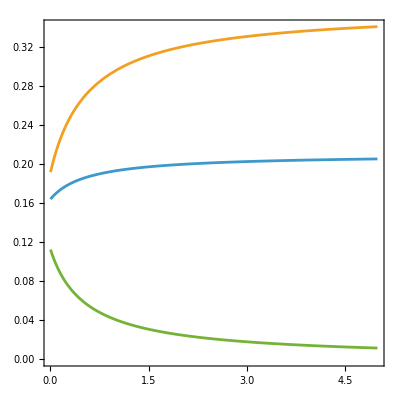

```mathematica
Plot[{WA11[1/tsw],WAb[1/tsw],WAbb[1/tsw]},{tsw,0.001,5},Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1]
```

## Распределения при различных l_sw

```mathematica
(* ================================================================= *)
(* TOTAL DISTRIBUTION A: 4 parameter families x 3 switching lengths   *)
(* Evaluate AFTER the four-argument nine-state switchData[...] model. *)
(* Each curve is the physical PDF in Mb^-1 conditional on L >= Lcut.  *)
(* ================================================================= *)

ClearAll[
  aswL, aswBase, aswSD, aswFloors, aswOffsets, aswSwitchRatios,
  aswLcut, aswLmax, aswValues, aswParams, aswPDFExpr,
  aswFamilyNames, aswLegendValue, aswStyles, aswMakePlot,
  aswPlots, aswGamma005, aswGamma020, aswGamma050,
  aswGbEff005, aswGbEff020, aswGbEff050,
  aswAlpha005, aswAlpha020, aswAlpha050,
  aswLp005, aswLp020, aswLp050
];

If[Length[DownValues[switchData]] == 0,
  Print["First evaluate the nine-state switchData model."];
  Abort[]
];

If[!ValueQ[FSize], FSize = 18];
If[!ValueQ[FTicksSize], FTicksSize = 15];
FTicksSize = 20;

(* Same central estimates and +/- 1 SD as in the peak analysis. *)
aswBase = <|"Gamma" -> 2.7, "GbEff" -> 1.8,
            "Alpha" -> 1.2, "Lp" -> 0.431|>;
aswSD = <|"Gamma" -> 0.8, "GbEff" -> 0.7,
          "Alpha" -> 1.3, "Lp" -> 0.099|>;
aswFloors = <|"Gamma" -> 0.0001, "GbEff" -> 0.,
              "Alpha" -> 0., "Lp" -> 0.0001|>;
aswOffsets = {-1., -0.5, 0., 0.5, 1.};
aswSwitchRatios = {0.001,0.05, 0.2, 0.5};  (* s = l_sw/l_p *)

(* Physical length axis (Mb), necessary to show variation in l_p. *)
aswLcut = 0;    (* Mb: same conditioning as the peak plots *)
aswLmax = 0.800;    (* Mb: change if the long-length tail is needed *)

aswValues[key_String] := DeleteDuplicates @ Sort @ Table[
  Max[aswFloors[key], aswBase[key] + u aswSD[key]],
  {u, aswOffsets}
];
aswParams[key_String, value_?NumericQ] :=
  Join[aswBase, <|key -> value|>];

(* Return a symbolic function of the physical loop length L in Mb.    *)
(* Do NOT use switchNorm["A",...]: here we normalize to the same     *)
(* survival probability above 15.8 kb used by pkTheoryPeak.          *)
aswPDFExpr[L_Symbol, sw_?NumericQ, pp_Association] := Module[
  {d, mu, co, lp, gbBare, survival},
  lp = pp["Lp"];
  gbBare = pp["GbEff"] (1. + pp["Alpha"]);
  d = Quiet @ Check[
    switchData[1./sw, pp["Gamma"], gbBare, pp["Alpha"]],
    $Failed
  ];
  If[!AssociationQ[d], Return[$Failed]];
  mu = d["Eigenvalues"];
  co = d["Coefficients"]["A"];
  survival = N[Re[Chop[Total[-(co/mu) Exp[mu aswLcut/lp]]]]];
  If[!NumericQ[survival] || !TrueQ[survival > 0.],
    Return[$Failed]
  ];
  Re[Total[co Exp[mu L/lp]]]/(lp survival)
];

aswFamilyNames = <|
  "Gamma" -> "γ",
  "GbEff" -> Subscript["γ", "b,eff"],
  "Alpha" -> "α",
  "Lp" -> Subscript["l", "p"]
|>;

aswLegendValue[key_String, v_?NumericQ] :=
  If[key === "Lp",
    Row[{Round[1000 v]}],
    NumberForm[v, {4, 2}]
  ];

(* Rainbow runs from lowest to highest parameter value; in each      *)
(* family, the same five colors are used for all three sw values.     *)
aswStyles[n_Integer] := Table[
  Directive[
    ColorData[{"DarkRainbow", "Reverse"}][
      1. - N[i - 1]/Max[n - 1, 1]
    ],
    AbsoluteThickness[If[i == Ceiling[n/2], 3.0, 1.8]]
  ],
  {i, n}
];

aswMakePlot[key_String, sw_?NumericQ] := Module[
  {vals, curves, styles, labels, heading},
  vals = aswValues[key];
  curves = Table[
    aswPDFExpr[aswL, sw, aswParams[key, value]],
    {value, vals}
  ];
  If[MemberQ[curves, $Failed],
    Print["Could not evaluate distribution A for ", key,
          ", switching ratio ", sw];
    Return[$Failed]
  ];
  styles = aswStyles[Length[vals]];
  labels = aswLegendValue[key, #] & /@ vals;
  heading = Row[{
    aswFamilyNames[key], " variation,   ",
    Subscript["l", "sw"], "/", Subscript["l", "p"],
    " = ", NumberForm[sw, {3, 2}]
  }];

  Plot[
    Evaluate[curves],
    {aswL, aswLcut, aswLmax},
    Frame -> True,
    Axes -> False,
    AspectRatio -> 1,
    FrameStyle -> Directive[FSize, FontFamily -> "CMU Serif", Black],
    FrameTicksStyle -> Directive[FTicksSize, FontFamily -> "CMU Serif", Black],
    FrameTicks -> {{Range[0, 8, 2], None}, {Range[0, 0.8, 0.2], None}},
    PlotStyle -> styles,
    PlotRange -> All,
    PlotPoints -> 100,
    MaxRecursion -> 3,
    ImageSize -> 250
  ]
];

(* Compute each of the 12 graphics separately, WITHOUT a Grid/Show. *)
aswPlots = AssociationMap[
  Function[key,
    Association @ Table[sw -> aswMakePlot[key, sw],
      {sw, aswSwitchRatios}]
  ],
  {"Gamma", "GbEff", "Alpha", "Lp"}
];

aswGamma005 = aswPlots["Gamma"][0.05];
aswGamma020 = aswPlots["Gamma"][0.2];
aswGamma050 = aswPlots["Gamma"][0.5];

aswGbEff005 = aswPlots["GbEff"][0.05];
aswGbEff020 = aswPlots["GbEff"][0.2];
aswGbEff050 = aswPlots["GbEff"][0.5];

aswAlpha005 = aswPlots["Alpha"][0.05];
aswAlpha020 = aswPlots["Alpha"][0.2];
aswAlpha050 = aswPlots["Alpha"][0.5];

aswLp005 = aswPlots["Lp"][0.05];
aswLp020 = aswPlots["Lp"][0.2];
aswLp050 = aswPlots["Lp"][0.5];

(* ================================================================= *)
(* Separate, continuous color bars for the 4 A-distribution families.  *)
(* Evaluate AFTER the asw... definitions from the 12-plot script.     *)
(* Exactly reproduces the five colors used by aswStyles, INCLUDING   *)
(* the clipped alpha=0 endpoint (uneven parameter spacing).           *)
(* ================================================================= *)

ClearAll[
  aswLegendInterpolator, aswLegendColor, aswMakeColorBar,
  aswLegends, aswLegendGamma, aswLegendGbEff,
  aswLegendAlpha, aswLegendLp
];

(* Map the five actual parameter values onto evenly spaced palette   *)
(* coordinates 0, 1/4, 1/2, 3/4, 1, as used by aswStyles.            *)
aswLegendInterpolator = AssociationMap[
  Function[key,
    Module[{values = aswValues[key], n},
      n = Length[values];
      Interpolation[
        Transpose[{values, N[Range[0, n - 1]/(n - 1)]}],
        InterpolationOrder -> 1
      ]
    ]
  ],
  {"Gamma", "GbEff", "Alpha", "Lp"}
];

aswLegendColor[key_String, value_?NumericQ] :=
  ColorData[{"DarkRainbow", "Reverse"}][
    1. - Clip[aswLegendInterpolator[key][value], {0., 1.}]
  ];

aswMakeColorBar[key_String] := Module[
  {values, lo, hi, ticks},
  values = aswValues[key];
  lo = First[values];
  hi = Last[values];
  ticks = ({#, aswLegendValue[key, #]} & /@ values);

  With[{family = key, low = lo, high = hi, marks = ticks},
    DensityPlot[
      y, {u, 0, 1}, {y, low, high},
      (* DensityPlot passes only the density value z to ColorFunction. *)
      ColorFunction -> Function[z,
        aswLegendColor[family, z]
      ],
      ColorFunctionScaling -> False,
      Mesh -> None,
      PlotPoints -> 70,
      MaxRecursion -> 0,
      AspectRatio -> 10,
      Frame -> True,
      FrameTicks -> {{None, marks}, {None, None}},
      FrameStyle -> Directive[10, FontFamily -> "CMU Serif", Black],
      FrameTicksStyle -> Directive[18, FontFamily -> "CMU Serif", Black],
      RotateLabel -> False,
      ImageSize -> {105, 280},
		ImagePadding -> {{5, 55}, {10, 10}},
      PlotRangePadding -> None
    ]
  ]
];

(* Four INDEPENDENT graphics, not a combined panel. *)
aswLegends = AssociationMap[
  aswMakeColorBar, {"Gamma", "GbEff", "Alpha", "Lp"}
];
aswLegendGamma = aswLegends["Gamma"];
aswLegendGbEff = aswLegends["GbEff"];
aswLegendAlpha = aswLegends["Alpha"];
aswLegendLp = aswLegends["Lp"];

(* Show one at a time: *)
(* aswLegendGamma *)
(* aswLegendGbEff *)
(* aswLegendAlpha *)
(* aswLegendLp *)

(* Optional exports: *)
(* Export["A_gamma_legend.pdf", aswLegendGamma]; *)
(* Export["A_gbeff_legend.pdf", aswLegendGbEff]; *)
(* Export["A_alpha_legend.pdf", aswLegendAlpha]; *)
(* Export["A_lp_legend.pdf", aswLegendLp]; *)
```

```mathematica
aswGbEff2 = aswPlots["GbEff"][0.001];
```

```mathematica
aswGamma2 = aswPlots["Gamma"][0.001];
```

```mathematica
aswLp2 = aswPlots["Lp"][0.001];
```

```mathematica
aswAlpha2 = aswPlots["Alpha"][0.001];
```

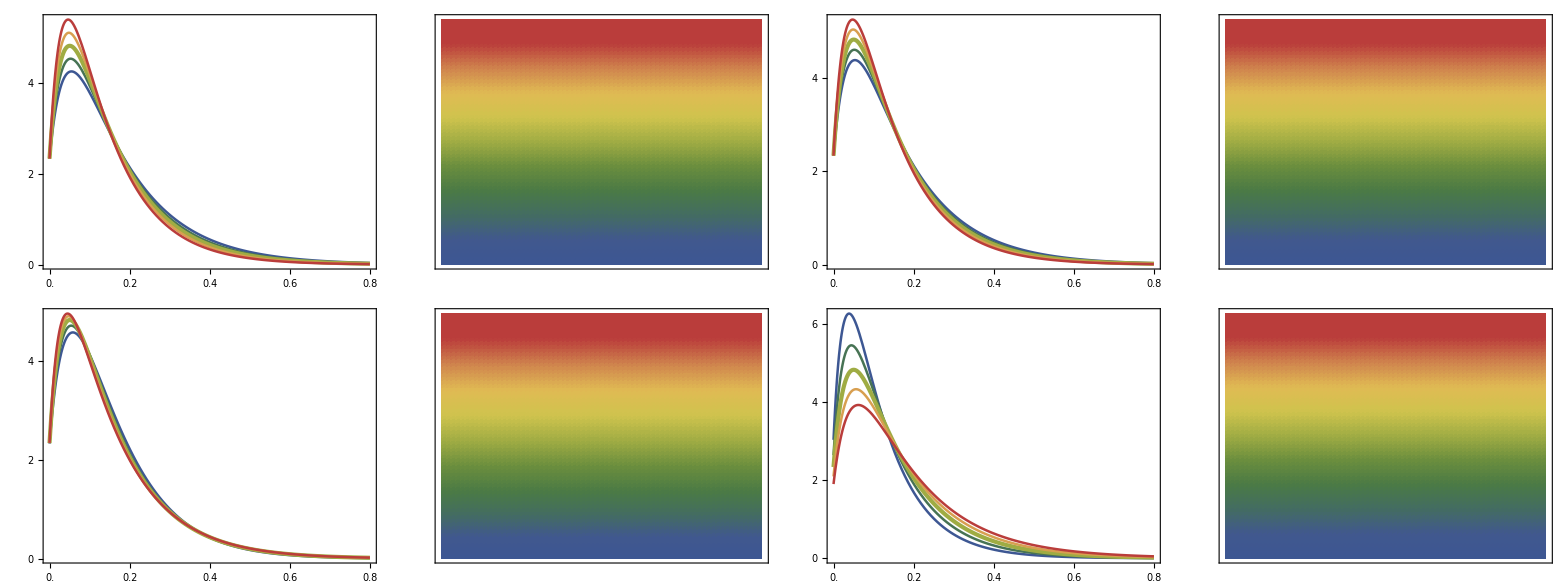

```mathematica
aswFigure2x2=Grid[{{aswAlignedPlot[aswGbEff2],aswAlignedLegend[aswLegendGbEff],aswAlignedPlot[aswGamma2],aswAlignedLegend[aswLegendGamma]},{aswAlignedPlot[aswAlpha2],aswAlignedLegend[aswLegendAlpha],aswAlignedPlot[aswLp2],aswAlignedLegend[aswLegendLp]}},Alignment->{Center,Top},Spacings->{{0.2,2.0,0.2},1.5}];

aswFigure2x2
```

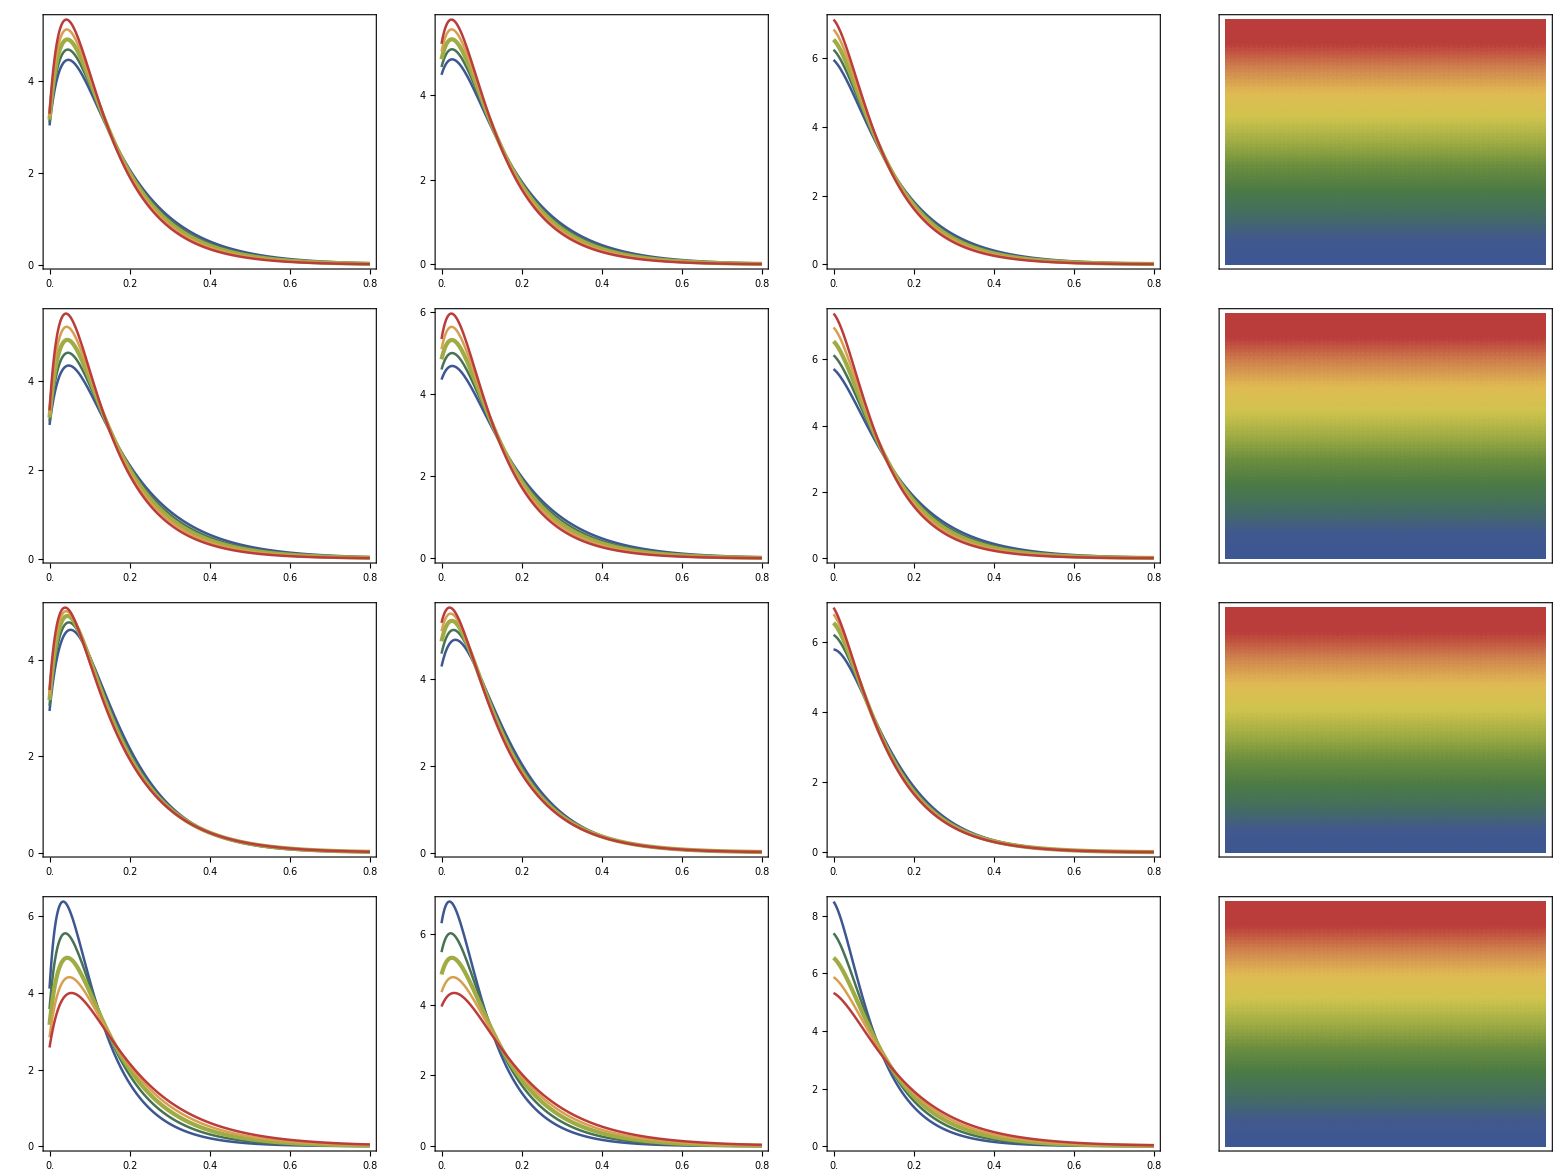

```mathematica
ClearAll[aswAlignedPlot,aswAlignedLegend,aswFigure];

(*Main plots:frame area 240 x 240*)
aswAlignedPlot[g_]:=Show[g,ImageSize->{280,280},AspectRatio->1,ImagePadding->{{34,20},{30,10}}];

(*Legends:frame area 30 x 240*)
aswAlignedLegend[g_]:=Show[g,ImageSize->{110,280},AspectRatio->8,ImagePadding->{{8,72},{30,10}},PlotRangePadding->None];

aswFigure=Grid[{{aswAlignedPlot[aswGamma005],aswAlignedPlot[aswGamma020],aswAlignedPlot[aswGamma050],aswAlignedLegend[aswLegendGamma]},{aswAlignedPlot[aswGbEff005],aswAlignedPlot[aswGbEff020],aswAlignedPlot[aswGbEff050],aswAlignedLegend[aswLegendGbEff]},{aswAlignedPlot[aswAlpha005],aswAlignedPlot[aswAlpha020],aswAlignedPlot[aswAlpha050],aswAlignedLegend[aswLegendAlpha]},{aswAlignedPlot[aswLp005],aswAlignedPlot[aswLp020],aswAlignedPlot[aswLp050],aswAlignedLegend[aswLegendLp]}},Alignment->{Center,Top},Spacings->{0.6,0.7}];

aswFigure
```

## Загрузка эксперимента

```mathematica
ClearAll[importLoopLengthTable];
folder="C:\\петли\\ЭКСПЕРИМЕНТЫ\\данные для гистограмм\\rad21\\";

(*Находим PET-expanded файлы*)
files=Sort@FileNames["*_loop_lengths_pet_expanded.csv",folder];

(*Импорт одного файла:только колонка span_kb*)
importLoopLengthTable[file_]:=Module[{data,header,lengthColumn,values},data=Import[file,"CSV"];
header=First[data];
lengthColumn=First@FirstPosition[header,"span_kb"];
values=Rest[data][[All,lengthColumn]];
(*Одноколоночная таблица:{{длина1},{длина2},...}*)List/@N[values]];

(*Ассоциация:название файла->таблица длин*)
loopLengthTables=AssociationThread[FileBaseName/@files,importLoopLengthTable/@files];

(*Пять отдельных таблиц*)
{K562rep1,K562rep2,K562rep3,GMrep1,GMrep2}=Values[loopLengthTables];
```

```mathematica
GMrep1=Flatten[GMrep1]/1000;
```

```mathematica
GMrep2=Flatten[GMrep2]/1000;
```

```mathematica
Subscript["l","sw"]
```

l_sw

```mathematica
4.8/5.5
```

0.872727

## АНализ пика

```mathematica
(* ==================================================================== *)
(* POISSON SWITCHING: PEAK POSITION VS PEAK AMPLITUDE                   *)
(*                                                                    *)
(* Run after defining switchData[beta, gamma, gbBare, alpha] in the     *)
(* nine-state model, and two raw datasets GMrep1 and GMrep2 in Mb.     *)
(*                                                                    *)
(* THEORY: continuous maximum on L >= 0, normalized by the survival   *)
(*         probability above Lcut = 0.0158 Mb.                         *)
(* EXP:    2 separate 30-kb histogram peaks; each has its own         *)
(*         multinomial bootstrap standard deviations in X and Y.     *)
(* PLOTS:  four parameter families varying only ONE independently     *)
(*         estimated model parameter per panel.                       *)
(* COLOR:  l_sw/l_p (same palette and range in every panel).          *)
(* ==================================================================== *)

ClearAll[
  pkLp0, pkLcut, pkBinWidth, pkSearchMax, pkSwGrid, pkNBoot,
  pkReplicates, pkRepData, pkNBins, pkLend, pkBinEdges, pkBinCenters,
  pkBinCounts, pkPeakFromCounts, pkBootstrapStats, pkRepStats, pkRepColors,
  pkGamma0, pkGbEff0, pkAlpha0, pkBaseParams, pkSpecs, pkOffsets,
  pkParamValues, pkTheoryPeak, pkCentralRows, pkFamilyRows, pkFamilies,
  pkColor, pkStyledSegments, pkModelPoints, pkAllModelPoints,
  pkAllX, pkAllY, pkCommonRange, pkExpPlots, pkFamilyPlot,
  pkPanels, pkPanelGamma, pkPanelGbEff, pkPanelAlpha, pkPanelLp,
  pkColorBar, pkColorMin, pkColorMax, pkColorTicks, pkNColors,
  pkFourPanelFigure, pkExpLegend, pkSlopeGrid
];

(* 1. INPUT DATA AND SETTINGS *)
If[!ValueQ[GMrep1] || !ValueQ[GMrep2],
  Print["Please define GMrep1 and GMrep2 (lists of loop lengths in Mb)."];
  Abort[]
];
If[Length[DownValues[switchData]] == 0,
  Print["Please evaluate the nine-state switchData model first."];
  Abort[]
];
lswmax = 0.5;

pkReplicates = {GMrep1, GMrep2};
pkLp0 = 0.431;                (* Mb = 431 kb *)
pkLcut = 0.0158;              (* Mb = 15.8 kb *)
pkBinWidth = 0.015;           (* Mb = 30 kb; change to 0.015 if needed *)
pkSearchMax = 0.600;          (* Mb; continuous theoretical peak search *)
pkSwGrid = N[Range[0.001, 0.501, 0.01]];
pkNBoot = 500;
SeedRandom[20261120];

pkRepData = (
  Select[Flatten[{#}], NumericQ[#] && TrueQ[# >= pkLcut] &] &
) /@ pkReplicates;
If[!And @@ (Length[#] > 1 & /@ pkRepData),
  Print["At least one replicate has too few observations above 15.8 kb."];
  Abort[]
];

pkNBins = Ceiling[(pkSearchMax - pkLcut)/pkBinWidth];
pkLend = pkLcut + pkNBins pkBinWidth;
pkBinEdges = N[Table[pkLcut + j pkBinWidth, {j, 0, pkNBins}]];
pkBinCenters = MovingAverage[pkBinEdges, 2];

(* 2. EXPERIMENT: SAME FIXED HISTOGRAM BINS IN BOTH REPLICATES. *)
(* Multinomial bootstrap of the bin counts is exactly equivalent to  *)
(* resampling the raw observations with replacement for THIS statistic. *)
(* One extra category contains all observed lengths beyond the last  *)
(* displayed bin, so PDF normalization uses all loops above the cutoff. *)

pkBinCounts[data_List] := BinCounts[
  data, {pkLcut, pkLend, pkBinWidth}
];

pkPeakFromCounts[counts_List, n_Integer] := Module[{k},
  k = First[Ordering[counts, -1]];
  {pkBinCenters[[k]], N[counts[[k]]/(n pkBinWidth)]}
];

pkBootstrapStats[data_List] := Module[
  {n, counts, otherCount, probs, samples, bootstrapPeaks,
   observedPeak, sigma, intervalX, intervalY},

  n = Length[data];
  counts = pkBinCounts[data];
  otherCount = n - Total[counts];
  probs = N[Append[counts, otherCount]/n];

  observedPeak = pkPeakFromCounts[counts, n];
  samples = RandomVariate[MultinomialDistribution[n, probs], pkNBoot];
  bootstrapPeaks = (
    pkPeakFromCounts[Take[#, pkNBins], n] &
  ) /@ samples;

  sigma = StandardDeviation /@ Transpose[bootstrapPeaks];
  intervalX = Quantile[bootstrapPeaks[[All, 1]], {0.16, 0.84}];
  intervalY = Quantile[bootstrapPeaks[[All, 2]], {0.16, 0.84}];

  <|
    "N" -> n,
    "Peak" -> observedPeak,
    "BootstrapSD" -> sigma,
    "Bootstrap68Range" -> {intervalX, intervalY},
    "BootstrapPeaks" -> bootstrapPeaks
  |>
];

pkRepStats = pkBootstrapStats /@ pkRepData;
pkRepColors = {Blue, RGBColor[0.5, 0, 0.5]};

Print["Experimental peaks (Mb, Mb^-1) and separate bootstrap errors:"];
Print[Grid[
  Prepend[
    Table[
      {
        "Rep. " <> ToString[i],
        pkRepStats[[i]]["N"],
        NumberForm[1000 pkRepStats[[i]]["Peak"][[1]], {7, 2}],
        NumberForm[1000 pkRepStats[[i]]["BootstrapSD"][[1]], {7, 2}],
        NumberForm[pkRepStats[[i]]["Peak"][[2]], {7, 3}],
        NumberForm[pkRepStats[[i]]["BootstrapSD"][[2]], {7, 3}]
      },
      {i, 2}
    ],
    {"Replicate", "N", "Lpeak, kb", "SD(Lpeak), kb", "Apeak, Mb^-1", "SD(Apeak)"}
  ], Frame -> All
]];

If[AnyTrue[pkRepStats, #["BootstrapSD"][[1]] == 0 &],
  Print["NOTE: Zero bootstrap SD in X means the peak stayed in the same",
        " histogram bin; it does NOT imply perfect positional resolution."]
];

(* 3. INDEPENDENTLY ESTIMATED PARAMETERS AND THEIR UNCERTAINTIES. *)
(* Ranges taken from the Supplementary Materials, Tables params/nondim. *)
(* gbBare = gbEff (1 + alpha) is recalculated in each model call.       *)
(* For alpha, the nonphysical negative endpoint is clipped to zero.  *)

pkGamma0 = 2.7;
pkGbEff0 = 1.8;
pkAlpha0 = 1.2;

pkBaseParams = <|
  "Gamma" -> pkGamma0,
  "GbEff" -> pkGbEff0,
  "Alpha" -> pkAlpha0,
  "Lp" -> pkLp0
|>;

pkSpecs = <|
  "Gamma" -> <|"SD" -> 0.8,   "Floor" -> 0.0001,
     "Title" -> "Cohesin density,  γ"|>,
  "GbEff" -> <|"SD" -> 0.7,   "Floor" -> 0.,
     "Title" -> "Barrier density,  γ_(<b>)"|>,
  "Alpha" -> <|"SD" -> 1.3,   "Floor" -> 0.,
     "Title" -> "Barrier persistence,  α"|>,
  "Lp"    -> <|"SD" -> 0.099, "Floor" -> 0.0001,
     "Title" -> "Processivity,  l_(<p>)"|>
|>;

(* Five model curves for each parameter: low, intermediate, central, ... *)
pkOffsets = {-1., -0.5, 0., 0.5, 1.};

pkParamValues[key_String] := Sort @ DeleteDuplicates @ Table[
  Max[pkSpecs[key]["Floor"],
      pkBaseParams[key] + u pkSpecs[key]["SD"]],
  {u, pkOffsets}
];

(* 4. THEORY: INDEPENDENT FOUR-PARAMETER switchData CALL. *)
(* Peak position is found for L >= 0, but the amplitude is always     *)
(* normalized by the integrated model probability above 15.8 kb.    *)
(* No theoretical binning is performed.                              *)

pkTheoryPeak[sw_?NumericQ, pp_Association] := Module[
  {be, d, mu, co, thisLp, bareBarrier, survival,
   f, df, grid, pairs, brackets, roots, rr,
   z, a, b, fa, fb, br, candidates, best},

  be = 1./sw;
  thisLp = pp["Lp"];
  bareBarrier = pp["GbEff"] (1. + pp["Alpha"]);
  d = Quiet @ Check[
    switchData[be, pp["Gamma"], bareBarrier, pp["Alpha"]],
    $Failed
  ];
  If[!AssociationQ[d], Return[$Failed]];

  mu = d["Eigenvalues"];
  co = d["Coefficients"]["A"];
  survival = N[Re[Chop[Total[-(co/mu) Exp[mu pkLcut/thisLp]]]]];
  If[!NumericQ[survival] || !TrueQ[survival > 0.], Return[$Failed]];

  f[t_?NumericQ] :=
    N[Re[Total[co Exp[mu t/thisLp]]]/(thisLp survival)];
  df[t_?NumericQ] :=
    N[Re[Total[(co mu) Exp[mu t/thisLp]]]/(thisLp^2 survival)];

  (* Dense near zero, coarser beyond 60 kb. *)
  grid = N[Join[
    Subdivide[0., 0.060, 80],
    Rest[Subdivide[0.060, pkSearchMax, 90]]
  ]];
  pairs = Partition[Transpose[{grid, df /@ grid}], 2, 1];
  brackets = Cases[
    pairs,
    {{a_?NumericQ, fa_?NumericQ}, {b_?NumericQ, fb_?NumericQ}} /;
      TrueQ[fa fb < 0] :> {a, b}
  ];

  roots = Table[
    rr = Quiet @ Check[
      z /. FindRoot[df[z] == 0,
        {z, Mean[br], br[[1]], br[[2]]},
        AccuracyGoal -> 9, PrecisionGoal -> 9,
        MaxIterations -> 80],
      Missing["RootFailure"]
    ];
    rr,
    {br, brackets}
  ];
  roots = Select[
    roots,
    NumericQ[#] && TrueQ[0. <= # <= pkSearchMax] &
  ];

  candidates = ({#, f[#]} &) /@ Join[{0., pkSearchMax}, roots];
  If[!AllTrue[candidates[[All, 2]], NumericQ], Return[$Failed]];
  best = First @ MaximalBy[candidates, Last];

  <|
    "sw" -> sw,
    "Lpeak" -> best[[1]],
    "Apeak" -> best[[2]],
    "Survival" -> survival,
    "AtZero" -> TrueQ[Abs[best[[1]]] < 10^-7],
    "AtUpperBound" -> TrueQ[Abs[best[[1]] - pkSearchMax] < 10^-7]
  |>
];

(* 5. THE FOUR ONE-AT-A-TIME PARAMETER FAMILIES. *)
(* The central profile is computed once and reused in all panels. *)
Print["Calculating the central theoretical trajectory..."];
pkCentralRows = DeleteCases[
  (pkTheoryPeak[#, pkBaseParams] &) /@ pkSwGrid,
  $Failed
];

pkFamilyRows[key_String] := Table[
  Module[{params, isCenter, rows},
    params = Join[pkBaseParams, <|key -> value|>];
    isCenter = TrueQ[Abs[value - pkBaseParams[key]] < 10^-10];
    rows = If[isCenter, pkCentralRows,
      DeleteCases[(pkTheoryPeak[#, params] &) /@ pkSwGrid, $Failed]
    ];
    <|"Parameter" -> key, "Value" -> value,
      "Central" -> isCenter, "Rows" -> rows|>
  ],
  {value, pkParamValues[key]}
];

pkFamilies = Association[];
Do[
  Print["Calculating variation in ", key, " ..."];
  AssociateTo[pkFamilies, key -> pkFamilyRows[key]],
  {key, Keys[pkSpecs]}
];

If[AnyTrue[Flatten[Values[pkFamilies], 1],
   Length[#["Rows"]] < 2 &],
  Print["WARNING: Some parameter profiles have fewer than 2 valid points."]
];

If[AnyTrue[
   Flatten[Lookup[Flatten[Values[pkFamilies], 1], "Rows"], 1],
   #["AtUpperBound"] &],
  Print["WARNING: Some maxima reach the upper search boundary;",
        " consider increasing pkSearchMax."]
];

(* 6. A COMMON PLOT RANGE FOR ALL FOUR PANELS. *)
pkModelPoints[rows_List] := ({#["Lpeak"], #["Apeak"]} &) /@ rows;
pkAllModelPoints = Flatten[
  (pkModelPoints[#["Rows"]] &) /@ Flatten[Values[pkFamilies], 1],
  1
];

pkAllX = Join[
  pkAllModelPoints[[All, 1]],
  Flatten[Table[
    pkRepStats[[i]]["Peak"][[1]] +
      {-1, 1} pkRepStats[[i]]["BootstrapSD"][[1]],
    {i, 2}
  ]]
];
pkAllY = Join[
  pkAllModelPoints[[All, 2]],
  Flatten[Table[
    pkRepStats[[i]]["Peak"][[2]] +
      {-1, 1} pkRepStats[[i]]["BootstrapSD"][[2]],
    {i, 2}
  ]]
];
pkCommonRange = {
  {Max[0., Min[pkAllX] - 0.005], Max[pkAllX] + 0.005},
  {Max[0., Min[pkAllY] - 0.35], Max[pkAllY] + 0.35}
};

(* ================================================================ *)
(* INDEPENDENT PEAK PANELS AND COLOR BAR                              *)
(* Run AFTER pkFamilies, pkRepStats, pkBaseParams, pkSpecs,            *)
(* pkCentralRows, pkCommonRange and pkModelPoints have been computed. *)
(* No Grid is evaluated. Every plot can be displayed independently.  *)
(* ================================================================ *)

ClearAll[
  swColor, pkColor, pkStyledSegments, pkExpPlots, pkFamilyPlot,
  pkPanelGamma, pkPanelGbEff, pkPanelAlpha, pkPanelLp, pkPanels,
  pkColorBar, pkColorBarKb, pkNColors, pkInsetLines, pkInsetPlot
];

(* All curves, including the inset, use this SAME function. *)
lswmax = 0.5;
swColor[s_?NumericQ] :=
  ColorData[{"DarkRainbow", "Reverse"}][Exp[-3.0 s/lswmax]];
pkColor[s_?NumericQ] := swColor[s];

pkStyledSegments[rows_List, opacity_?NumericQ, width_?NumericQ] :=
 Module[{pts, segments, styles},
  pts = pkModelPoints[rows];
  If[Length[pts] < 2, Return[{{}, {}}]];
  segments = Partition[pts, 2, 1];
  styles = Table[
    Directive[
      pkColor[Mean[{rows[[i]]["sw"], rows[[i + 1]]["sw"]}]],
      Opacity[opacity], AbsoluteThickness[width]
    ],
    {i, Length[segments]}
  ];
  {segments, styles}
];

(* Two experimental replicates and their original error bars. *)
pkExpPlots = Table[
  With[{p = pkRepStats[[i]]["Peak"],
        sd = pkRepStats[[i]]["BootstrapSD"],
        col = pkRepColors[[i]]},
    ListPlot[
      {{Around[p[[1]], pkBinWidth/2], Around[p[[2]], sd[[2]]]}},
      PlotStyle -> Directive[col, PointSize[0.015]]
    ]
  ],
  {i, 2}
];

(* Return one Graphics object, never a Grid/Row/Column. *)
pkFamilyPlot[key_String] := Module[
  {ordered, bundles, segments, styles, model},
  ordered = Join[
    Select[pkFamilies[key], !#["Central"] &],
    Select[pkFamilies[key], #["Central"] &]
  ];
  bundles = Table[
    pkStyledSegments[
      entry["Rows"],
      If[entry["Central"], 1., 0.33],
      If[entry["Central"], 3.3, 1.7]
    ],
    {entry, ordered}
  ];
  segments = Flatten[bundles[[All, 1]], 1];
  styles = Flatten[bundles[[All, 2]], 1];
  model = ListLinePlot[
    segments,
    PlotStyle -> styles,
    Frame -> True, Axes -> False,
    PlotRange -> pkCommonRange,
    PlotRangePadding -> None,
    FrameLabel -> {{Superscript["Peak amplitude, Mb", "-1"],    None},  {
    "Peak position, Mb",pkSpecs[key]["Title"]}},
    FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],
    FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],
    AspectRatio -> 1,
    ImageSize -> {450, 345}
  ];
  Show[
    model, Sequence @@ pkExpPlots,
    PlotRange -> pkCommonRange,
    PlotRangePadding -> None,
    AspectRatio -> 1,
    ImageSize -> {450, 345}
  ]
];

(* Four genuinely separate Graphics objects. *)
pkPanelGamma = pkFamilyPlot["Gamma"];
pkPanelGbEff = pkFamilyPlot["GbEff"];
pkPanelAlpha = pkFamilyPlot["Alpha"];
pkPanelLp = pkFamilyPlot["Lp"];

(* Keep an optional association for convenient lookup. *)
pkPanels = <|
  "Gamma" -> pkPanelGamma,
  "GbEff" -> pkPanelGbEff,
  "Alpha" -> pkPanelAlpha,
  "Lp" -> pkPanelLp
|>;

(* Single raster-based color bar: no Rectangle seam artifacts. *)
pkNColors = 500;
pkColorBar = Graphics[
  {
    Raster[
      Table[
        {List @@ swColor[(i - 0.5) lswmax/pkNColors]},
        {i, 1, pkNColors}
      ],
      {{0, 0}, {1, lswmax}}
    ]
  },
  PlotRange -> {{0, 1}, {0, lswmax}},
  PlotRangePadding -> None,
  Frame -> True,
  FrameTicks -> {
    {None, Table[{s, NumberForm[s, {2, 1}]}, {s, 0., 0.5, 0.1}]},
    {None, None}
  },
  FrameStyle -> Directive[18, Black, FontFamily -> "CMU Serif"],
  FrameTicksStyle -> Directive[15, Black, FontFamily -> "CMU Serif"],
  PlotLabel -> Style["l_sw / l_p", 15, FontFamily -> "CMU Serif"],
  AspectRatio -> 9,
  ImagePadding -> {{3, 50}, {8, 8}},
  ImageSize -> {105, 350}
];

(* Optional second bar labelled in physical kb for the central lp.  *)
(* Do not use the kb bar to interpret curves where lp was varied.     *)
pkColorBarKb = Show[
  pkColorBar,
  FrameTicks -> {
    {None, Table[{L/(1000. pkLp0), L}, {L, 0, 200, 50}]},
    {None, None}
  },
  PlotLabel -> Style["l_sw, kb", 13,
    FontFamily -> "CMU Serif"]
];

(* A compact central-parameters-only inset, same colors and error bars. *)
pkInsetLines = pkStyledSegments[pkCentralRows, 1., 3.3];
pkInsetPlot = Show[
  ListLinePlot[
    pkInsetLines[[1]],
    PlotStyle -> pkInsetLines[[2]],
    Frame -> True,
    Axes -> False
  ],
  Sequence @@ pkExpPlots,
  PlotRange -> {{0, 0.065}, {4.5, 7}},
  PlotRangePadding -> None,
  PlotRangeClipping -> True,
  Frame -> True,
  Axes -> False,
  FrameTicks -> {
    {{{5, "5"}, {6, "6"}}, None},
    {{{0, "0"}, {0.035, "0.035"}}, None}
  },
  FrameStyle -> Directive[Black, FontFamily -> "Times"],
  FrameTicksStyle -> Directive[14, FontFamily -> "Times"],
  AspectRatio -> 1,
  ImagePadding -> {{36, 8}, {30, 6}},
  ImageSize -> 150
];

(* Display separately by evaluating any ONE of the following:       *)
(* pkPanelGamma   pkPanelGbEff   pkPanelAlpha   pkPanelLp            *)
(* pkColorBar     pkColorBarKb  pkInsetPlot                         *)
(* Example export: Export["pk_gamma.pdf", pkPanelGamma];            *)

Print["Ready: pkPanelGamma, pkPanelGbEff, pkPanelAlpha, pkPanelLp, pkColorBar, pkColorBarKb, pkInsetPlot"];
```

Experimental peaks (Mb, Mb^-1) and separate bootstrap errors:

Replicate | N | Lpeak, kb | SD(Lpeak), kb | Apeak, Mb^-1 | SD(Apeak)
Rep. 1 | 90863 | 53.30 | 3.27 | 5.461 | 0.058
Rep. 2 | 64176 | 53.30 | 3.21 | 4.766 | 0.065

Calculating the central theoretical trajectory...

Calculating variation in Gamma ...

Calculating variation in GbEff ...

Calculating variation in Alpha ...

Calculating variation in Lp ...

Ready: pkPanelGamma, pkPanelGbEff, pkPanelAlpha, pkPanelLp, pkColorBar, pkColorBarKb, pkInsetPlot

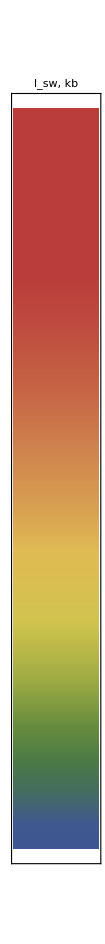

```mathematica
pkColorBarKb
```

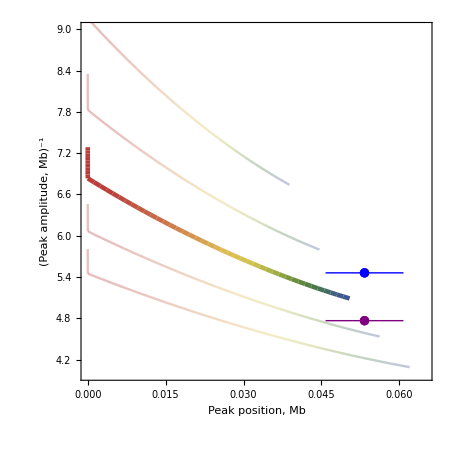

```mathematica
Show[pkPanelLp,PlotRange->{{0,0.065},{4,9}}]
```

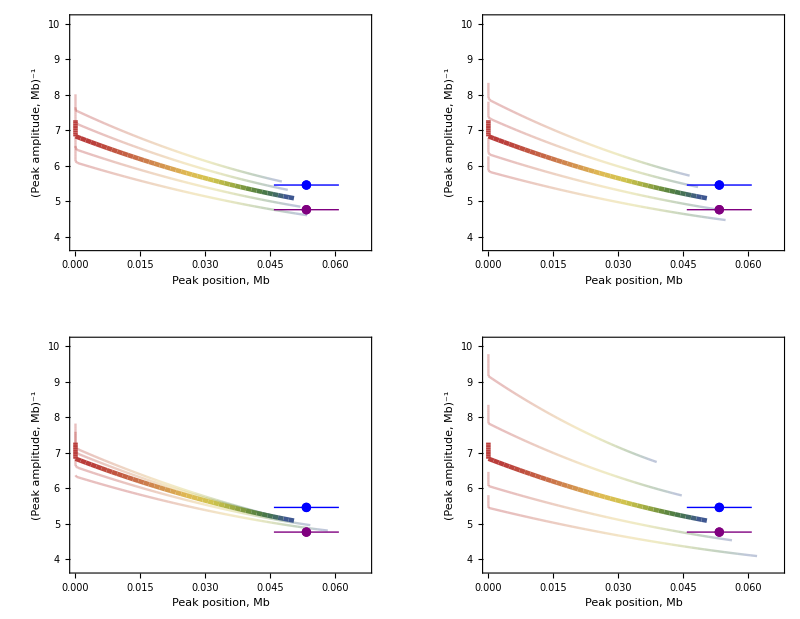

```mathematica
GraphicsGrid[{{pkPanelGamma,pkPanelGbEff},{pkPanelAlpha,pkPanelLp}}]
```

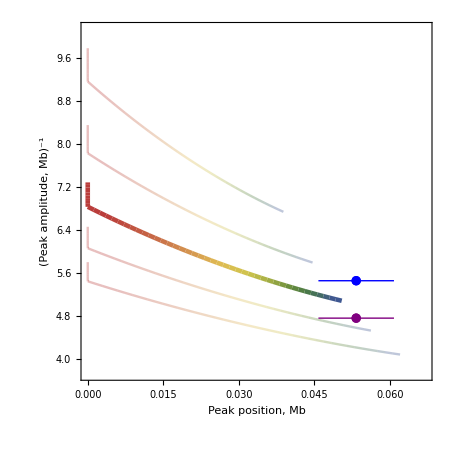

```mathematica
pkPanelLp
```

```mathematica
(* =================================================================== *)
(* CRITICAL l_sw: FIRST POSITION EXIT + AMPLITUDE COMPATIBILITY            *)
(* Run AFTER pkFamilies, pkBaseParams, pkRepStats, pkTheoryPeak, pkSwGrid.  *)
(*                                                                         *)
(* First identify the switching length at which the global theoretical   *)
(* peak position moves below the experimental lower position bound.      *)
(* THEN evaluate the SAME theoretical peak at that switching length, and *)
(* accept the threshold only if its amplitude lies between the two        *)
(* observed experimental peak amplitudes.                                 *)
(*                                                                         *)
(* Values failing the amplitude test are EXCLUDED from family means,     *)
(* but their position-only thresholds and rejection reasons are retained. *)
(* The amplitude condition uses an empirical inter-replicate envelope,    *)
(* not a bootstrap confidence interval.                                   *)
(* =================================================================== *)

ClearAll[
  crSigmaMode, crXError, crRepBounds, crReferences,
  crAmplitudeBounds, crAmplitudeTolerance,
  crRefine, crRatioTolerance, crCriticalPoint,
  crDetails, crStats, crSummary, crFmt,
  crBothDetails, crFamilyKeys, crFamilyLabels,
  crBothSummary, crPlotData, crSummaryPlot
];

If[!AssociationQ[pkFamilies] || !AssociationQ[pkBaseParams] ||
   !ListQ[pkRepStats] || Length[pkRepStats] != 2,
  Print["First evaluate the original model code through pkFamilies / pkRepStats."];
  Abort[]
];

(* 1. POSITION AND AMPLITUDE CONSTRAINTS. *)
crSigmaMode = "Displayed";
(* "Displayed": half the bin width (7.5 kb for 15-kb bins). *)
(* "Bootstrap": bootstrap SD of peak position.               *)
(* "Conservative": maximum of the two.                        *)

crXError[i_Integer] := Switch[crSigmaMode,
  "Displayed", pkBinWidth/2,
  "Bootstrap", pkRepStats[[i]]["BootstrapSD"][[1]],
  "Conservative", Max[pkBinWidth/2,
    pkRepStats[[i]]["BootstrapSD"][[1]]],
  _, pkBinWidth/2
];

crRepBounds = AssociationThread[
  {"Rep1", "Rep2"},
  Table[pkRepStats[[i]]["Peak"][[1]] - crXError[i], {i, 2}]
];
AssociateTo[crRepBounds, "Both" -> Min[Values[crRepBounds]]];
crReferences = {"Both", "Rep1", "Rep2"};

(* Amplitude = the PDF height (Mb^-1) of the experimental peak. *)
(* Use the same amplitude envelope for all three position criteria. *)
crAmplitudeBounds = MinMax[
  Table[pkRepStats[[i]]["Peak"][[2]], {i, 2}]
];
crAmplitudeTolerance = 0.; (* optional numerical tolerance in Mb^-1 *)

If[!VectorQ[crAmplitudeBounds, NumericQ] ||
   !TrueQ[crAmplitudeBounds[[1]] <= crAmplitudeBounds[[2]]],
  Print["Invalid experimental peak amplitudes."];
  Abort[]
];

Print["Position lower bounds (kb): ",
  AssociationMap[1000 crRepBounds[#] &, crReferences]];
Print["Allowed experimental peak amplitude range (Mb^-1): ",
  crAmplitudeBounds];

(* 2. FIRST DOWNWARD POSITION CROSSING WITH REFINED MODEL EVALUATION. *)
crRefine = True;
crRatioTolerance = 0.0002; (* absolute tolerance for l_sw / l_p *)

crCriticalPoint[rows_List, lower_?NumericQ, params_Association] := Module[
  {base, valid, crossing, lo, hi, ylo, yhi, interpolated,
   mid, trial, result, sCrit, n = 0, lp, amplitude, status},

  lp = params["Lp"];
  base = <|
    "PositionOnlyRatio" -> Missing["NotFound"],
    "PositionOnlyKb" -> Missing["NotFound"],
    "LpeakAtExitKb" -> Missing["NotFound"],
    "PeakAmplitudeAtExit" -> Missing["NotFound"],
    "AmplitudeOK" -> False,
    "CriticalRatio" -> Missing["NoAcceptedCriticalPoint"],
    "CriticalKb" -> Missing["NoAcceptedCriticalPoint"],
    "Status" -> "NotEvaluated"
  |>;

  valid = SortBy[
    Select[rows,
      AssociationQ[#] && NumericQ[#["sw"]] &&
        NumericQ[#["Lpeak"]] && NumericQ[#["Apeak"]] &
    ],
    #["sw"] &
  ];
  If[Length[valid] < 2,
    Return[Join[base, <|"Status" -> "TooFewModelPoints"|>]]
  ];
  If[TrueQ[valid[[1]]["Lpeak"] < lower],
    Return[Join[base, <|"Status" -> "AlreadyBelowAtFirstPoint"|>]]
  ];

  crossing = SelectFirst[
    Partition[valid, 2, 1],
    (#[[1]]["Lpeak"] >= lower && #[[2]]["Lpeak"] < lower) &,
    Missing["NoCrossingInScanRange"]
  ];
  If[MissingQ[crossing],
    Return[Join[base, <|"Status" -> "NoCrossingInScanRange"|>]]
  ];

  {lo, hi} = Lookup[crossing, "sw"];
  {ylo, yhi} = Lookup[crossing, "Lpeak"];
  If[hi - lo > 1.5 Min[Differences[pkSwGrid]],
    Return[Join[base, <|"Status" -> "GapInModelGrid"|>]]
  ];

  interpolated = N[lo + (lower - ylo) (hi - lo)/(yhi - ylo)];
  sCrit = interpolated;

  If[TrueQ[crRefine],
    (* Bisection: works even if the global maximum jumps between modes. *)
    While[hi - lo > crRatioTolerance && n < 40,
      mid = (lo + hi)/2.;
      trial = Quiet @ Check[pkTheoryPeak[mid, params], $Failed];
      If[!AssociationQ[trial] || !NumericQ[trial["Lpeak"]] ||
         !NumericQ[trial["Apeak"]],
        Return[Join[base, <|"Status" -> "RefinementFailed"|>]]
      ];
      If[trial["Lpeak"] < lower, hi = mid, lo = mid];
      n++;
    ];
    sCrit = N[hi];
  ];

  (* Critical step: recalculate BOTH Lpeak and Apeak at EXACTLY sCrit. *)
  result = Quiet @ Check[pkTheoryPeak[sCrit, params], $Failed];
  If[!AssociationQ[result] || !NumericQ[result["Lpeak"]] ||
     !NumericQ[result["Apeak"]],
    Return[Join[base, <|"Status" -> "FinalModelEvaluationFailed"|>]]
  ];

  (* Interpolation-only mode can land just inside the position interval. *)
  If[!TrueQ[result["Lpeak"] < lower] && !TrueQ[crRefine],
    sCrit = N[hi];
    result = Quiet @ Check[pkTheoryPeak[sCrit, params], $Failed]
  ];
  If[!AssociationQ[result] || !NumericQ[result["Lpeak"]] ||
     !NumericQ[result["Apeak"]],
    Return[Join[base, <|"Status" -> "FinalModelEvaluationFailed"|>]]
  ];
  If[!TrueQ[result["Lpeak"] < lower],
    Return[Join[base, <|"Status" -> "PositionNotOutside"|>]]
  ];

  amplitude = N[result["Apeak"]];
  status = Which[
    amplitude < crAmplitudeBounds[[1]] - crAmplitudeTolerance,
      "AmplitudeBelowRange",
    amplitude > crAmplitudeBounds[[2]] + crAmplitudeTolerance,
      "AmplitudeAboveRange",
    True, "OK"
  ];

  Join[base, <|
    "PositionOnlyRatio" -> sCrit,
    "PositionOnlyKb" -> 1000 lp sCrit,
    "LpeakAtExitKb" -> 1000 result["Lpeak"],
    "PeakAmplitudeAtExit" -> amplitude,
    "AmplitudeOK" -> (status === "OK"),
    "CriticalRatio" -> If[status === "OK", sCrit,
      Missing["AmplitudeRejected"]],
    "CriticalKb" -> If[status === "OK", 1000 lp sCrit,
      Missing["AmplitudeRejected"]],
    "Status" -> status
  |>]
];

(* 3. COMPUTE EACH PARAMETER VALUE FOR BOTH AND INDIVIDUAL REPLICATES. *)
crDetails = Flatten[
  Table[
    Module[{entry, params, crit},
      entry = pkFamilies[family][[j]];
      params = Join[pkBaseParams, <|family -> entry["Value"]|>];
      crit = crCriticalPoint[
        entry["Rows"], crRepBounds[reference], params
      ];
      Join[
        <|"Reference" -> reference, "Family" -> family,
          "ParameterValue" -> entry["Value"],
          "Central" -> entry["Central"]|>,
        crit
      ]
    ],
    {reference, crReferences},
    {family, Keys[pkFamilies]},
    {j, Length[pkFamilies[family]]}
  ],
  2
];

(* 4. FAMILY STATS: rejected thresholds do not enter means / SDs. *)
crStats[values_List] := Module[{v, n},
  v = N @ Select[values, NumericQ];
  n = Length[v];
  <|
    "N" -> n,
    "Mean" -> If[n >= 1, Mean[v], Missing["NoValues"]],
    "SD" -> If[n >= 2, StandardDeviation[v], Missing["NeedTwoValues"]],
    "SEM" -> If[n >= 2,
      StandardDeviation[v]/Sqrt[n], Missing["NeedTwoValues"]]
  |>
];

crSummary = Flatten[
  Table[
    Module[{subset, ratios, lengths, statuses},
      subset = Select[crDetails,
        #["Reference"] === reference && #["Family"] === family &
      ];
      ratios = crStats[Lookup[subset, "CriticalRatio"]];
      lengths = crStats[Lookup[subset, "CriticalKb"]];
      statuses = Lookup[subset, "Status"];
      <|
        "Reference" -> reference,
        "Family" -> family,
        "NpositionCrossings" -> Count[
          Lookup[subset, "PositionOnlyRatio"], _?NumericQ],
        "Nvalid" -> ratios["N"],
        "NrejectedAmplitude" -> Count[
          statuses, "AmplitudeBelowRange" | "AmplitudeAboveRange"],
        "Nmissing" -> Length[subset] - ratios["N"],
        "MeanRatio" -> ratios["Mean"],
        "SDRatio" -> ratios["SD"],
        "SEMRatio" -> ratios["SEM"],
        "MeanKb" -> lengths["Mean"],
        "SDKb" -> lengths["SD"],
        "SEMKb" -> lengths["SEM"]
      |>
    ],
    {reference, crReferences},
    {family, Keys[pkFamilies]}
  ],
  1
];

crFmt[x_, decimals_: 3] := If[
  NumericQ[x], NumberForm[x, {9, decimals}], "--"
];
crBothDetails = Select[crDetails, #["Reference"] === "Both" &];

Print["POSITION crossing and AMPLITUDE check, each parameter (both replicates):"];
Print[Grid[
  Prepend[
    ({#["Family"], crFmt[#["ParameterValue"], 3],
      crFmt[#["PositionOnlyRatio"], 4],
      crFmt[#["PositionOnlyKb"], 2],
      crFmt[#["LpeakAtExitKb"], 2],
      crFmt[#["PeakAmplitudeAtExit"], 3],
      crFmt[#["CriticalRatio"], 4],
      crFmt[#["CriticalKb"], 2],
      #["Status"]} & /@ crBothDetails),
    {"Family", "Parameter", "Position-only ratio", "Position-only kb",
     "Lpeak at exit, kb", "Apeak at exit, Mb^-1", "Accepted ratio",
     "Accepted kb", "Status"}
  ],
  Frame -> All, Alignment -> Center
]];

Print["Family summary: only BOTH position and amplitude constraints count:"];
Print[Grid[
  Prepend[
    ({#["Reference"], #["Family"],
      #["NpositionCrossings"], #["Nvalid"],
      #["NrejectedAmplitude"], #["Nmissing"],
      crFmt[#["MeanRatio"], 4], crFmt[#["SDRatio"], 4],
      crFmt[#["SEMRatio"], 4],
      crFmt[#["MeanKb"], 2], crFmt[#["SDKb"], 2],
      crFmt[#["SEMKb"], 2]} & /@ crSummary),
    {"Reference", "Family", "Position exits", "Accepted", "Amp rejected",
     "Missing", "Mean ratio", "SD ratio", "SEM ratio",
     "Mean kb", "SD kb", "SEM kb"}
  ],
  Frame -> All, Alignment -> Center
]];

(* Inspect machine-readable data: Dataset[crDetails]; Dataset[crSummary] *)

(* 5. PLOT: mean +/- sample SD of accepted thresholds (joint position). *)
crFamilyKeys = {"Gamma", "GbEff", "Alpha", "Lp"};
crFamilyLabels = {"γ", "γb,eff", "α", "lp"};
crBothSummary = Table[
  SelectFirst[crSummary,
    #["Reference"] === "Both" && #["Family"] === family &
  ],
  {family, crFamilyKeys}
];

crPlotData = DeleteCases[
  MapIndexed[
    If[NumericQ[#1["MeanRatio"]] && NumericQ[#1["SDRatio"]],
      {First[#2], Around[#1["MeanRatio"], #1["SDRatio"]]},
      Nothing
    ] &,
    crBothSummary
  ],
  Nothing
];

crSummaryPlot = If[Length[crPlotData] > 0,
  ListPlot[
    crPlotData,
    Frame -> True, Axes -> False,
    FrameTicks -> {
      {Automatic, None},
      {Thread[Range[Length[crFamilyKeys]] -> crFamilyLabels], None}
    },
    FrameLabel -> {"Varied parameter", "Critical l_sw/l_p (mean +/- SD)"},
    PlotMarkers -> {Automatic, 12},
    PlotRange -> All,
    PlotRangePadding -> Scaled[0.12],
    ImageSize -> 560,
    PlotLabel -> "Position exits both replicates AND amplitude is compatible"
  ],
  Style["No families with 2+ accepted critical values", Darker[Red]]
];
crSummaryPlot

(* Optional CSV export of accepted statistics and diagnostic statuses: *)
(* Export["critical_lsw_with_amplitude_details.csv",
    Prepend[
      (Lookup[#, {"Reference", "Family", "ParameterValue",
         "PositionOnlyRatio", "PositionOnlyKb", "PeakAmplitudeAtExit",
         "CriticalRatio", "CriticalKb", "Status"}] & /@ crDetails),
      {"Reference", "Family", "ParameterValue", "PositionOnlyRatio",
       "PositionOnlyKb", "PeakAmplitudeAtExit", "CriticalRatio",
       "CriticalKb", "Status"}
    ]
   ]; *)

(* Optional CSV export of the family summary: *)
(* Export["critical_lsw_with_amplitude_summary.csv",
     Prepend[
       (Lookup[#, {"Reference", "Family", "NpositionCrossings",
          "Nvalid", "NrejectedAmplitude", "Nmissing", "MeanRatio",
          "SDRatio", "SEMRatio", "MeanKb", "SDKb", "SEMKb"}] & /@ crSummary),
       {"Reference", "Family", "NpositionCrossings", "Nvalid",
        "NrejectedAmplitude", "Nmissing", "MeanRatio", "SDRatio",
        "SEMRatio", "MeanKb", "SDKb", "SEMKb"}
     ]
   ]; *)
```

Position lower bounds (kb): <|Both→1000 (-0.0075+BinCounts[{},{0.0158,0.6008,0.015}]),Rep1→1000 (-0.0075+BinCounts[{},{0.0158,0.6008,0.015}]),Rep2→1000 (-0.0075+BinCounts[{},{0.0158,0.6008,0.015}])|>

Allowed experimental peak amplitude range (Mb^-1): {0,0}

Join::incpt: Incompatible elements in Join[<|Reference→Both,Family→Gamma,ParameterValue→1.9,Central→False|>,crCriticalPoint[«1»]] cannot be joined.

Join::incpt: Incompatible elements in Join[<|Reference→Both,Family→Gamma,ParameterValue→2.3,Central→False|>,crCriticalPoint[«1»]] cannot be joined.

Join::incpt: Incompatible elements in Join[<|Reference→Both,Family→Gamma,ParameterValue→2.7,Central→True|>,crCriticalPoint[{<|sw→0.001,Lpeak→0.0504284,Apeak→5.08875,Survival→0.949534,AtZero→False,AtUpperBound→False|>,<|sw→0.011,Lpeak→0.049217,Apeak→5.11632,Survival→0.947354,AtZero→False,AtUpperBound→False|>,<|sw→0.021,Lpeak→0.0479991,Apeak→5.14484,Survival→0.945273,AtZero→False,AtUpperBound→False|>,<|sw→0.031,Lpeak→0.0467756,Apeak→5.17428,Survival→0.943286,AtZero→False,AtUpperBound→False|>,«44»,<|sw→0.481,Lpeak→0.,Apeak→7.19413,Survival→0.899435,AtZero→True,AtUpperBound→False|>,<|sw→0.491,Lpeak→0.,Apeak→7.24121,Survival→0.898949,AtZero→True,AtUpperBound→False|>,«1»},-«7»+«1»,<|Gamma→2.7,GbEff→1.8,Alpha→1.2,Lp→0.431|>]] cannot be joined.

General::stop: Further output of Join::incpt will be suppressed during this calculation.

POSITION crossing and AMPLITUDE check, each parameter (both replicates):

Family | Parameter | Position-only ratio | Position-only kb | Lpeak at exit, kb | Apeak at exit, Mb^-1 | Accepted ratio | Accepted kb | Status

Family summary: only BOTH position and amplitude constraints count:

Reference | Family | Position exits | Accepted | Amp rejected | Missing | Mean ratio | SD ratio | SEM ratio | Mean kb | SD kb | SEM kb
Both | Gamma | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Both | GbEff | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Both | Alpha | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Both | Lp | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep1 | Gamma | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep1 | GbEff | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep1 | Alpha | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep1 | Lp | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep2 | Gamma | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep2 | GbEff | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep2 | Alpha | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --
Rep2 | Lp | 0 | crStats[Missing[KeyAbsent,CriticalRatio]][N] | 0 | -crStats[Missing[KeyAbsent,CriticalRatio]][N] | -- | -- | -- | -- | -- | --

No families with 2+ accepted critical values

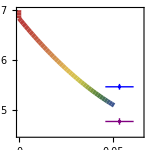

```mathematica
pkInsetLines=pkStyledSegments[pkCentralRows,1.,3.3];

pkInsetPlot=Show[ListLinePlot[pkInsetLines[[1]],PlotStyle->pkInsetLines[[2]],Frame->True,Axes->False,PlotRange->{{0,0.06},{4.5,7}},PlotRangePadding->None,FrameStyle->Directive[12,FontFamily->"Times",Black],FrameTicksStyle->Directive[17],FrameTicks->{{{{5,"5"},{6,"6"},{7,"7"}},None},{{{0,"0"},{0.025,"0.025"},{0.05,"0.05"}},None}},FrameTicksStyle->Directive[12,FontFamily->"Times"],AspectRatio->1],Sequence@@pkExpPlots,PlotRange->{{0,0.065},{4.5,7}},PlotRangePadding->None,AspectRatio->1,ImagePadding->{{36,6},{30,6}},ImageSize->150];

pkInsetPlot
```

```mathematica
GMrad21rep1=GMrep1;
GMrad21rep2=GMrep2;
```

```mathematica
ClearAll[kCut,kMax,kRep1,kRep2,kData,kH0,kKernel,kFactors,kPeak,kResults,kExpPoints,kExpPlot];

(*1. Parameters*)

kCut=0.0158;     (*Mb*)
kMax=0.20;       (*Mb;peak search region*)

kRep1=N@Select[Flatten[{GMrad21rep1}],NumericQ[#]&&TrueQ[#>=kCut]&];

kRep2=N@Select[Flatten[{GMrad21rep2}],NumericQ[#]&&TrueQ[#>=kCut]&];

kData={kRep1,kRep2};

(*2. Common bandwidth for both replicates*)

kPool=Join[kRep1,kRep2];
kQuartiles=Quantile[kPool,{0.25,0.75}];

kH0=0.9 Min[StandardDeviation[kPool],(kQuartiles[[2]]-kQuartiles[[1]])/1.34] Length[kPool]^(-1/5);

kKernel={"Bounded",{kCut,Infinity},"Gaussian"};

(*Bandwidth sensitivity*)
kFactors={0.7,0.85,1.0,1.15,1.3};

(*3. Find peak of the smooth density*)

kPeak[data_,hh_]:=Module[{dist,grid,vals,idx},dist=SmoothKernelDistribution[data,hh,kKernel];
grid=N@Subdivide[kCut,kMax,4000];
vals=N[PDF[dist,#]&/@grid];
idx=First@Ordering[vals,-1];
{grid[[idx]],vals[[idx]]}];

(*4. Peak and sensitivity for each replicate*)

kResults=Table[Module[{p0,variants,err},p0=kPeak[kData[[i]],kH0];
variants=Table[kPeak[kData[[i]],factor kH0],{factor,kFactors}];
err=Table[Max[Abs[variants[[All,j]]-p0[[j]]]],{j,2}];
<|"Peak"->p0,"Error"->err,"Variants"->variants|>],{i,2}];

(*5. Print results*)

Print["Bandwidth = ",N[1000 kH0,4]," kb"];

TableForm[Table[{i,1000 kResults[[i]]["Peak"][[1]],1000 kResults[[i]]["Error"][[1]],kResults[[i]]["Peak"][[2]],kResults[[i]]["Error"][[2]]},{i,2}],TableHeadings->{None,{"Replicate","Lpeak, kb","dL, kb","Apeak, Mb^-1","dA, Mb^-1"}}]
```

Bandwidth = 10.4132 kb

Replicate | Lpeak, kb | dL, kb | Apeak, Mb^-1 | dA, Mb^-1
1 | 58.0739 | 3.08535 | 5.44587 | 0.0789973
2 | 59.5475 | 6.03255 | 4.70928 | 0.0945631

KolmogorovSmirnovTest::ties: Ties exist in the data and will be ignored for the KolmogorovSmirnov test, which assumes unique values.

KDE 1 vs replicate 2: D = 0.0680159

KDE 2 vs replicate 1: D = 0.0831103

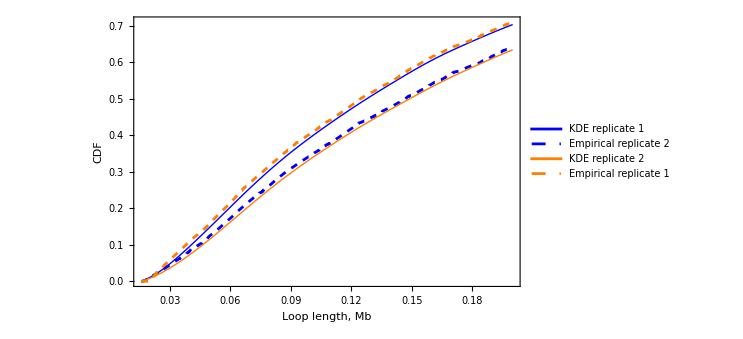

```mathematica
(*KDEs with the same bandwidth and boundary correction*)kdeD1=SmoothKernelDistribution[kRep1,kH0,kKernel];
kdeD2=SmoothKernelDistribution[kRep2,kH0,kKernel];

(*Compare KDE against the OTHER replicate*)

kdeD12=KolmogorovSmirnovTest[kRep2,kdeD1,"TestStatistic"];

kdeD21=KolmogorovSmirnovTest[kRep1,kdeD2,"TestStatistic"];

Print["KDE 1 vs replicate 2: D = ",kdeD12];
Print["KDE 2 vs replicate 1: D = ",kdeD21];

(*Empirical CDFs*)

empD1=EmpiricalDistribution[kRep1];
empD2=EmpiricalDistribution[kRep2];

Plot[Evaluate[{CDF[kdeD1,L],CDF[empD2,L],CDF[kdeD2,L],CDF[empD1,L]}],{L,kCut,kMax},PlotStyle->{Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Orange,Thick],Directive[Orange,Dashed]},Frame->True,Axes->False,FrameLabel->{"Loop length, Mb","CDF"},PlotLegends->{"KDE replicate 1","Empirical replicate 2","KDE replicate 2","Empirical replicate 1"},PlotRange->All,ImageSize->550]
```

```mathematica
ClearAll[kdePeakError];

kdePeakError[data_,dist_,hh_]:=Module[{peak,m,a,z,xx,fit,curvature,seL,seA,n},n=Length[data];
peak=kPeak[data,hh];
m=peak[[1]];
a=peak[[2]];
(*Local quadratic fit around the peak*)xx=Subdivide[Max[kCut,m-hh],m+hh,20];
fit=Fit[({#,PDF[dist,#]}&/@xx),{1,z,z^2},z];
curvature=2 Coefficient[fit,z,2];
seA=Sqrt[a/(2 Sqrt[Pi] n hh)];
seL=If[curvature<0,Sqrt[a/(4 Sqrt[Pi] n hh^3)]/Abs[curvature],Indeterminate];
<|"Lpeak"->m,"Apeak"->a,"SE_L"->seL,"SE_A"->seA,"Curvature"->curvature,"BoundaryDistanceOverH"->(m-kCut)/hh|>];

kdeErr1=kdePeakError[kRep1,kdeD1,kH0];
kdeErr2=kdePeakError[kRep2,kdeD2,kH0];

Dataset[{kdeErr1,kdeErr2}]
```

```mathematica
Superscript["Peak amplitude, Mb","-1"]
```

(Peak amplitude, Mb)^-1

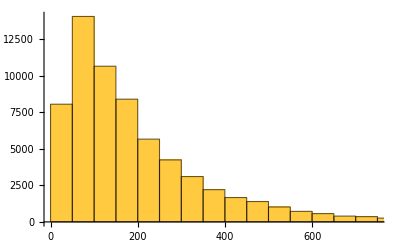

```mathematica
Histogram[Flatten[GMrep2]]
```

```mathematica
Histogram[GMrep1]
```

Part::partw: Part 2 of TerminatedEvaluation[] does not exist.

TerminatedEvaluation[IterationLimit]

```mathematica
(* =================================================================== *)
(* POISSON SWITCHING: peak position vs. peak amplitude                  *)
(* Two independent experimental KDE peaks with their own approximate  *)
(* fixed-bandwidth standard errors; no bootstrap and no binning.       *)
(* Family of rainbow-colored theoretical trajectories obtained by     *)
(* varying independently estimated model parameters within bounds.    *)
(*                                                                     *)
(* Theory: continuous peak sought for L >= 0; PDF amplitude divided   *)
(* by survival probability S(Lcut), with Lcut = 15.8 kb.                *)
(* Input: existing 4-argument switchData[beta,gamma,gammaB,alpha]      *)
(* and raw replicate loop lengths GMrep1 and GMrep2 (both in Mb).      *)
(* =================================================================== *)

ClearAll[
  pkCut, pkSearchMax, pkRootGridSize, pkSwGrid, pkNProfiles,
  pkRawReplicates, pkRepData, pkKDEKernel, pkKDEBandwidth,
  pkKDEPeak, pkKDEPeakError, pkKDEResults, pkExperimentalPoints,
  pkParamRanges, pkParamKeys, pkParamCenter, pkLatinU,
  pkSampleParam, pkParameterSamples, pkAllParameters,
  pkTheoryPeak, pkComputeProfile, pkProfiles, pkReferenceProfile,
  pkFamilyProfiles, pkColor, pkColorMin, pkColorMax,
  pkFamilySegments, pkFamilyStyles, pkReferenceSegments,
  pkReferenceStyles, pkAllXY, pkAllX, pkAllY, pkPlotRange,
  pkFamilyPlot, pkReferencePlot, pkExpPlot1, pkExpPlot2,
  pkCurvePlot, pkColorBar, pkNColors, pkColorTicks,
  pkFinalFigure, pkTable
];

(* -------- 1. Data and fixed plotting choices -------- *)

If[!ValueQ[GMrep1] || !ValueQ[GMrep2],
  Print["First define GMrep1 and GMrep2 as separate lists of loop lengths (Mb)."];
  Abort[]
];

pkRawReplicates = {GMrep1, GMrep2};
pkCut = 0.0158;              (* Mb, 15.8 kb: observation cutoff *)
pkSearchMax = 0.600;        (* Mb; continuous peak search [0,0.6] *)
pkRootGridSize = 120;       (* derivative-bracketing grid, not histogram bins *)
pkSwGrid = N[Range[0.001, 0.501, 0.01]]; (* sw = l_sw/l_p *)
pkNProfiles = 20;           (* number of noncentral parameter sets *)

(* Always normalize each KDE over ALL observed loops above pkCut. *)
pkRepData = (
  Select[Flatten[{#}], NumericQ[#] && TrueQ[# >= pkCut] &] &
) /@ pkRawReplicates;

If[!And @@ (Length[#] >= 10 & /@ pkRepData),
  Print["Too few valid loops above 15.8 kb in at least one replicate."];
  Abort[]
];

(* -------- 2. Two KDE peaks and separate error bars -------- *)
(* Same bandwidth for both replicas, fixed from pooled sample.         *)
(* These errors are asymptotic, fixed-bandwidth KDE standard errors,   *)
(* NOT KS distances and NOT a confidence interval for smoothing bias. *)

With[{pool = Join @@ pkRepData},
  pkKDEBandwidth = 0.9 Min[
    StandardDeviation[pool],
    (Subtract @@ Reverse[Quantile[pool, {0.25, 0.75}]])/1.34
  ] Length[pool]^(-1/5)
];

pkKDEKernel = {"Bounded", {pkCut, Infinity}, "Gaussian"};

pkKDEPeak[dist_] := Module[{grid, heights, ix},
  grid = N[Subdivide[pkCut, 0.20, 4000]];
  heights = N[(PDF[dist, #] &) /@ grid];
  ix = First[Ordering[heights, -1]];
  {grid[[ix]], heights[[ix]]}
];

pkKDEPeakError[data_List] := Module[
  {dist, pp, xm, ym, n, grid, fit, zz, curv, seX, seY},
  n = Length[data];
  dist = SmoothKernelDistribution[data, pkKDEBandwidth, pkKDEKernel];
  pp = pkKDEPeak[dist];
  xm = pp[[1]];
  ym = pp[[2]];

  (* Local quadratic approximation of the KDE curvature. *)
  grid = N[Subdivide[Max[pkCut, xm - pkKDEBandwidth],
                     xm + pkKDEBandwidth, 20]];
  fit = Fit[({#, PDF[dist, #]} & /@ grid), {1, zz, zz^2}, zz];
  curv = N[2 Coefficient[fit, zz, 2]];

  seY = Sqrt[ym/(2 Sqrt[Pi] n pkKDEBandwidth)];
  seX = If[NumericQ[curv] && curv < 0,
    Sqrt[ym/(4 Sqrt[Pi] n pkKDEBandwidth^3)]/Abs[curv],
    Indeterminate
  ];

  <|
    "Peak" -> pp,
    "SE" -> {seX, seY},
    "Curvature" -> curv,
    "PeakDistanceOverBandwidth" -> (xm - pkCut)/pkKDEBandwidth,
    "N" -> n
  |>
];

pkKDEResults = pkKDEPeakError /@ pkRepData;
If[!And @@ (VectorQ[#["SE"], NumericQ] & /@ pkKDEResults),
  Print["Could not estimate the KDE peak errors; inspect curvature and bandwidth."];
  Abort[]
];

pkExperimentalPoints = Lookup[pkKDEResults, "Peak"];

Print["KDE bandwidth (kb): ", N[1000 pkKDEBandwidth, 4]];
Print["Experimental KDE peaks {Lpeak Mb, Apeak Mb^-1}: ", pkExperimentalPoints];
Print["Their separate approximate {SE_L Mb, SE_A Mb^-1}: ",
  Lookup[pkKDEResults, "SE"]];
Print["Distance of KDE peaks from cutoff, in bandwidths: ",
  Lookup[pkKDEResults, "PeakDistanceOverBandwidth"]];

(* -------- 3. Independent parameter estimates and their errors -------- *)
(* Source: independent-parameter tables in Supplementary Materials.   *)
(* gamma = 2.7 +/- 0.8; gamma_b,eff = 1.8 +/- 0.7;                  *)
(* alpha = 1.2 +/- 1.3 (truncated at zero); lp = (431 +/- 99) kb.   *)
(* We scan the rectangular ranges, not a joint probabilistic CI.      *)
(* The kinetic equations take BARE gamma_b = gamma_b,eff (1+alpha).    *)

pkParamRanges = <|
  "Gamma" -> {1.9, 3.5},
  "GammaBEff" -> {1.1, 2.5},
  "Alpha" -> {0., 2.5},
  "Lp" -> {0.332, 0.530}                (* Mb *)
|>;

pkParamCenter = <|
  "Gamma" -> 2.7,
  "GammaBEff" -> 1.8,
  "Alpha" -> 1.2,
  "Lp" -> 0.431
|>;

pkParamKeys = Keys[pkParamRanges];

(* Reproducible Latin-hypercube sampling of the 4-D parameter box. *)
(* Each parameter is sampled across its full range; no fitting.    *)
pkLatinU = BlockRandom[
  SeedRandom[20261120];
  Transpose@Table[
    RandomSample[
      N[(Range[pkNProfiles] -
        RandomReal[{0., 1.}, pkNProfiles])/pkNProfiles]
    ],
    {Length[pkParamKeys]}
  ]
];

pkSampleParam[u_List] := AssociationThread[
  pkParamKeys,
  Table[
    With[{rr = pkParamRanges[pkParamKeys[[j]]]},
      rr[[1]] + u[[j]] (rr[[2]] - rr[[1]])
    ],
    {j, Length[pkParamKeys]}
  ]
];

pkParameterSamples = pkSampleParam /@ pkLatinU;
pkAllParameters = Prepend[pkParameterSamples, pkParamCenter];

(* -------- 4. Theoretical peak from the FULL continuous PDF -------- *)
(* The curve amplitude is rescaled by S(Lcut), even for a peak below  *)
(* Lcut; that is an explicit extrapolation of the underlying model.   *)
(* switchData must support 4 numeric arguments as in the shared code.  *)

pkTheoryPeak[sw_?NumericQ, pp_Association] := Module[
  {be, lp, gam, al, bareB, d, mu, co, s,
   f, df, grid, slopes, brackets, roots, candidates, best,
   t, z, root, a, b, fa, fb, br},

  be = 1./sw;
  lp = pp["Lp"];
  gam = pp["Gamma"];
  al = pp["Alpha"];
  bareB = pp["GammaBEff"] (1. + al);

  d = Quiet[Check[switchData[be, gam, bareB, al], $Failed]];
  If[!AssociationQ[d], Return[$Failed]];
  mu = d["Eigenvalues"];
  co = d["Coefficients"]["A"];
  If[!VectorQ[mu, NumericQ] || !VectorQ[co, NumericQ], Return[$Failed]];

  (* Analytic tail integral of the full, initially unit-normalized A. *)
  s = N[Re[Total[-(co/mu) Exp[mu pkCut/lp]]]];
  If[!NumericQ[s] || s <= 0., Return[$Failed]];

  f[t_?NumericQ] :=
    N[Re[Total[co Exp[mu t/lp]]]/(lp s)];
  df[t_?NumericQ] :=
    N[Re[Total[(co mu) Exp[mu t/lp]]]/(lp^2 s)];

  grid = N[Subdivide[0., pkSearchMax, pkRootGridSize]];
  slopes = df /@ grid;
  brackets = Cases[
    Partition[Transpose[{grid, slopes}], 2, 1],
    {{a_?NumericQ, fa_?NumericQ}, {b_?NumericQ, fb_?NumericQ}} /;
      TrueQ[fa fb < 0] :> {a, b}
  ];

  roots = Table[
    root = Quiet[Check[
      z /. FindRoot[
        df[z] == 0, {z, Mean[br], br[[1]], br[[2]]},
        AccuracyGoal -> 9, PrecisionGoal -> 9,
        MaxIterations -> 80
      ],
      Missing["RootFailure"]
    ]];
    root,
    {br, brackets}
  ];
  roots = Select[roots,
    NumericQ[#] && TrueQ[0. <= # <= pkSearchMax] &
  ];

  candidates = ({#, f[#]} & /@ Join[{0., pkSearchMax}, roots]);
  If[!AllTrue[candidates[[All, 2]], NumericQ], Return[$Failed]];
  best = First@MaximalBy[candidates, Last];

  <|
    "lsw" -> sw,
    "Lpeak" -> best[[1]],
    "Apeak" -> best[[2]],
    "Survival" -> s,
    "AtZero" -> (Abs[best[[1]]] < 10^-7),
    "AtUpperBound" -> (Abs[best[[1]] - pkSearchMax] < 10^-7)
  |>
];

pkComputeProfile[pp_Association] := Module[{rows},
  rows = DeleteCases[pkTheoryPeak[#, pp] & /@ pkSwGrid, $Failed];
  <|"Parameters" -> pp, "Rows" -> rows|>
];

Print["Computing ", Length[pkAllParameters],
  " trajectories x ", Length[pkSwGrid], " switching lengths..."];

pkProfiles = pkComputeProfile /@ pkAllParameters;
pkReferenceProfile = First[pkProfiles];
pkFamilyProfiles = Rest[pkProfiles];

Print["Successful points per trajectory: ",
  Length /@ Lookup[pkProfiles, "Rows"]];
If[AnyTrue[pkProfiles, Length[#["Rows"]] < 2 &],
  Print["WARNING: some trajectories contain fewer than two valid points."]
];
If[AnyTrue[pkProfiles,
   AnyTrue[#["Rows"], #["AtUpperBound"] &] &],
  Print["WARNING: some peaks are at the upper search limit; consider increasing pkSearchMax."]
];

(* -------- 5. Rainbow color encodes sw = l_sw / l_p -------- *)

pkColorMin = Min[pkSwGrid];
pkColorMax = Max[pkSwGrid];
pkColor[sw_?NumericQ] :=
  ColorData["DarkRainbow"][Rescale[sw, {pkColorMin, pkColorMax}]];

(* Create a colored segment for each adjacent pair along each curve. *)
pkFamilySegments = Flatten[
  Table[
    Partition[
      ({#["Lpeak"], #["Apeak"]} &) /@ prof["Rows"],
      2, 1
    ],
    {prof, pkFamilyProfiles}
  ],
  1
];

pkFamilyStyles = Flatten[
  Table[
    Table[
      Directive[
        pkColor[Mean[Lookup[prof["Rows"][[{i, i + 1}]], "lsw"]]],
        Opacity[0.25], AbsoluteThickness[1.3]
      ],
      {i, Length[prof["Rows"]] - 1}
    ],
    {prof, pkFamilyProfiles}
  ],
  1
];

pkReferenceSegments = Partition[
  ({#["Lpeak"], #["Apeak"]} &) /@ pkReferenceProfile["Rows"],
  2, 1
];
pkReferenceStyles = Table[
  Directive[
    pkColor[Mean[Lookup[pkReferenceProfile["Rows"][[{i, i + 1}]], "lsw"]]],
    Opacity[1.], AbsoluteThickness[3.2]
  ],
  {i, Length[pkReferenceSegments]}
];

(* Plot limits encompass ALL sampled predictions and both error bars. *)
pkAllXY = Join[
  Flatten[
    Table[
      ({#["Lpeak"], #["Apeak"]} &) /@ prof["Rows"],
      {prof, pkProfiles}
    ],
    1
  ],
  Flatten[
    Table[
      With[{p = pkKDEResults[[i]]["Peak"],
            se = pkKDEResults[[i]]["SE"]},
        {
          {p[[1]] - se[[1]], p[[2]] - se[[2]]},
          {p[[1]] + se[[1]], p[[2]] + se[[2]]}
        }
      ],
      {i, 2}
    ],
    1
  ]
];

pkAllX = pkAllXY[[All, 1]];
pkAllY = pkAllXY[[All, 2]];
pkPlotRange = {
  {Max[0., Min[pkAllX] - 0.005], Max[pkAllX] + 0.005},
  {Max[0., Min[pkAllY] - 0.25], Max[pkAllY] + 0.25}
};

(* -------- 6. Standard ListLinePlot + two individual KDE error bars -------- *)

pkFamilyPlot = ListLinePlot[
  pkFamilySegments,
  PlotStyle -> pkFamilyStyles,
  Frame -> True, Axes -> False,
  PlotRange -> pkPlotRange, PlotRangePadding -> None,
  FrameLabel -> {"Peak position, Mb", "(Peak amplitude, Mb)^-1"},
  FrameStyle -> Directive[17, Black, FontFamily -> "Times"],
  FrameTicksStyle -> Directive[14, FontFamily -> "Times"],
  AspectRatio -> 1, ImageSize -> {560, 430}
];

pkReferencePlot = ListLinePlot[
  pkReferenceSegments,
  PlotStyle -> pkReferenceStyles,
  PlotRange -> pkPlotRange, PlotRangePadding -> None
];

pkExpPlot1 = ListPlot[
  {{
    Around[pkKDEResults[[1]]["Peak"][[1]], pkKDEResults[[1]]["Peak"][[1]]*0.068],
    Around[pkKDEResults[[1]]["Peak"][[2]], pkKDEResults[[1]]["Peak"][[2]]*0.068]
  }},
  PlotStyle -> Directive[Black, PointSize[0.025]]
];

pkExpPlot2 = ListPlot[
  {{
    Around[pkKDEResults[[2]]["Peak"][[1]], pkKDEResults[[2]]["Peak"][[1]]*0.083],
    Around[pkKDEResults[[2]]["Peak"][[2]], pkKDEResults[[2]]["Peak"][[2]]*0.083]
  }},
  PlotStyle -> Directive[RGBColor[0.48, 0.16, 0.43], PointSize[0.025]]
];

pkCurvePlot = Show[
  pkFamilyPlot, pkReferencePlot, pkExpPlot1, pkExpPlot2,
  PlotRange -> pkPlotRange, PlotRangePadding -> None,
  AspectRatio -> 1, ImageSize -> {560, 430},
  Epilog -> {
    Text[Style["Rep. 1", 12, Black, FontFamily -> "Times"],
      Offset[{9, 12}, pkKDEResults[[1]]["Peak"]], {-1, 0}],
    Text[Style["Rep. 2", 12, RGBColor[0.48, 0.16, 0.43],
       FontFamily -> "Times"],
      Offset[{9, -10}, pkKDEResults[[2]]["Peak"]], {-1, 0}]
  }
];

(* Compact manual colorbar: exact same colors as plotted segments. *)
pkNColors = 180;
pkColorTicks = {{0.001, "0.001"}, {0.1, "0.1"},
                {0.2, "0.2"}, {0.3, "0.3"},
                {0.4, "0.4"}, {0.5, "0.5"}};

pkColorBar = Graphics[
  Table[
    {
      pkColor[pkColorMin + (i - 0.5)
        (pkColorMax - pkColorMin)/pkNColors],
      EdgeForm[None],
      Rectangle[
        {0., pkColorMin + (i - 1.)
          (pkColorMax - pkColorMin)/pkNColors},
        {1., pkColorMin + i
          (pkColorMax - pkColorMin)/pkNColors}
      ]
    },
    {i, pkNColors}
  ],
  PlotRange -> {{0, 1}, {pkColorMin, pkColorMax}},
  PlotRangePadding -> None,
  Frame -> True,
  FrameTicks -> {{None, pkColorTicks}, {None, None}},
  FrameTicksStyle -> Directive[12, FontFamily -> "Times"],
  FrameStyle -> Directive[Black, Thin],
  AspectRatio -> 6, ImagePadding -> {{2, 49}, {10, 10}},
  ImageSize -> {98, 335},
  PlotLabel -> Style["l_sw / l_p", 13, FontFamily -> "Times"]
];

pkFinalFigure = Row[{pkCurvePlot, Spacer[8], pkColorBar}];
pkFinalFigure

(* Optional: inspect the underlying parameter combinations and curves. *)
(* Dataset[pkParameterSamples] *)
(* Dataset[pkReferenceProfile["Rows"]] *)
(* Export["peak_parameter_family.pdf", pkFinalFigure]; *)
```

First define GMrep1 and GMrep2 as separate lists of loop lengths (Mb).

$Aborted

Too few valid loops above 15.8 kb in at least one replicate.

$Aborted

StandardDeviation::shlen: The argument {} should have at least two elements.

Quantile::empt: Argument {} should be a nonempty list.

Subtract::argrx: Subtract called with 0 arguments; 2 arguments are expected.

Power::infy: Infinite expression 1/0^(1/5) encountered.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{}] should be a vector or a matrix of real numbers or a valid TemporalData object.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical or could not be inverted.

Infinity::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

SmoothKernelDistribution::invldd: The input data SmoothKernelDistribution[{}] should be a vector or a matrix of real numbers or a valid TemporalData object.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical or could not be inverted.

Infinity::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

Could not estimate the KDE peak errors; inspect curvature and bandwidth.

$Aborted

KDE bandwidth (kb): ComplexInfinity

Experimental KDE peaks {Lpeak Mb, Apeak Mb^-1}: {{0.2,PDF[SmoothKernelDistribution[{},ComplexInfinity,{Bounded,{0.0158,∞},Gaussian}],0.2]},{0.2,PDF[SmoothKernelDistribution[{},ComplexInfinity,{Bounded,{0.0158,∞},Gaussian}],0.2]}}

Their separate approximate {SE_L Mb, SE_A Mb^-1}: {{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}}

Distance of KDE peaks from cutoff, in bandwidths: {0.,0.}

Computing 21 trajectories x 51 switching lengths...

Successful points per trajectory: {51,51,51,51,51,51,51,51,51,51,51,51,50,51,51,51,51,51,51,51,51}

General::prng: The value of the option PlotRange -> {{Indeterminate,Indeterminate},{Indeterminate,Indeterminate}} is not All, Full, Automatic, a positive machine number or an appropriate list of range specifications.

-Graphics--Graphics-

## Model

```mathematica
sol=DSolve[{A11'[x]==-(1+γ+γo)A11[x]+Ac[x]+α*Ao[x],
Ac'[x]==2γ *A11[x]-(4+2γo/(2+α)+1/3γ)Ac[x]+α*γ*Ao[x]/(2+α),
Ao'[x]==2γo*A11[x]+γo/(2+α)*Ac[x]-(2+2α+γo/(1+2α)+(1+α)/(2+α)γ)Ao[x],
A11[0]==1,Ac[0]==0,Ao[0]==0},{A11,Ac,Ao},x];
```

```mathematica
A11s2=(A11[x]/.sol)[[1]];
```

```mathematica
Acs2=(Ac[x]/.sol)[[1]];
```

```mathematica
Aos2=(Ao[x]/.sol)[[1]];
```

```mathematica
Accs2=Acs2*γ/6;
```

```mathematica
Aocs2=(Acs2*γo+Aos2*γ)/(2(2+α));
```

```mathematica
Aoos2=Aos2*γo/(2*(1+2α));
```

```mathematica
A2=Simplify[A11s2+Acs2+Aos2+Accs2+Aocs2+Aoos2];
```

```mathematica
modelRad=Ai*A2/.x->x/lp;
```

```mathematica
modelCTCF=Ai*Aoos2/.x->x/lp;
```

```mathematica
modelA11=Ai*A11s2/.x->x/lp;
```

```mathematica
modelA1=Ai*Aos2/.x->x/lp;
```

```mathematica
Simplify[Aos2/.x->x/lp/.γ->3.7/.γo->4/.α->1.2/.lp->1]
```

-1.04535 ⅇ^(-11.9403 x)+0.158338 ⅇ^(-9.20342 x)+0.887008 ⅇ^(-3.4098 x)

```mathematica
A11s2/.α->1.2/.γo->4/.γ->2.7
```

5.40749×10^-6 ⅇ^(-3.07647 x) (76088.2+107146. ⅇ^(-7.89445 x)+1694.62 ⅇ^(-5.40886 x))

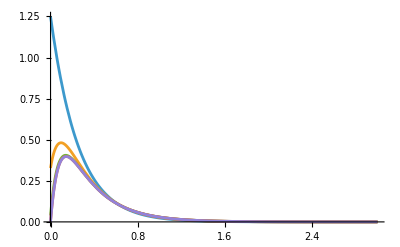

```mathematica
Plot[{AbF/.β->1,AbF/.β->10,AbF/.β->100,AbF/.β->1000,Simplify[Aos2/.x->x/lp/.γ->3.7/.γo->4/.α->1.2/.lp->1]},{x,0,3},PlotRange->All]
```

## Data

```mathematica
ExpPM=Import["C:\\Users\\kitte\\Downloads\\drive-download-20261104T075133Z-1-001\\contacts_3_both_extended_pm_distinct_motifs.csv","Data"][[2;;,30]]/10^6;
```

```mathematica
ExpPP=Import["C:\\Users\\kitte\\Downloads\\drive-download-20261104T075133Z-1-001\\contacts_3_both_extended_pp_distinct_motifs.csv","Data"][[2;;,30]]/10^6;
```

```mathematica
ExpMM=Import["C:\\Users\\kitte\\Downloads\\drive-download-20261104T075133Z-1-001\\contacts_3_both_extended_mm_distinct_motifs.csv","Data"][[2;;,30]]/10^6;
```

```mathematica
ExpMP=Import["C:\\Users\\kitte\\Downloads\\drive-download-20261104T075133Z-1-001\\contacts_3_both_extended_mp_distinct_motifs.csv","Data"][[2;;,30]]/10^6;
```

```mathematica
Length[ExpPM]
```

2456

```mathematica
Length[ExpFilteredf[ExpPM]]
```

2408

```mathematica
bins=Join[Range[0.001,0.01,0.002],Range[0.02,0.8,0.03]];
```

```mathematica
ExpFilteredf[Expf_]:=Table[If[Expf[[i]]>0.01,N[Expf[[i]]],Nothing],{i,1,Length[Expf]}];
```

```mathematica
Length[ExpFilteredf[ExpPP]]
```

60

```mathematica
Filtered=Join[ExpFilteredf[ExpPM],ExpFilteredf[ExpPP],ExpFilteredf[ExpMM],ExpFilteredf[ExpMP]];
```

```mathematica
hsDataf[Expf_]:=Module[{ExpFiltered,hsList,data},
ExpFiltered=Table[If[Expf[[i]]<0.01,N[Expf[[i]]],Nothing],{i,1,Length[Expf]}];
hsList=HistogramList[ExpFiltered,{0.001}];
data=Table[{(hsList[[1,i]]+hsList[[1,i+1]])/2,hsList[[2,i]]},{i,1,Length[hsList[[1]]]-1}];
data
]
```

```mathematica
Exp1=N[Flatten[Join[ExpPP,ExpMM]]];
```

```mathematica
bins2=Join[Range[0.001,0.01,0.003],Range[0.02,10,0.03]];
```

```mathematica
Integrate[(AbF/.β->100/.x->xi/0.431)*8+0.0025*xi^(-1.5),{xi,0.00022,10000}]
```

1.0034

```mathematica
Integrate[(AbF/.β->20/.x->xi/0.431)*7.5+0.0025*xi^(-1.5),{xi,0.00022,10000}]
```

1.00294

```mathematica
Integrate[(AbF/.β->20/.x->xi/0.431)*7.5+0.002*xi^(-1.5),{xi,0.001,0.01}]
```

0.103024

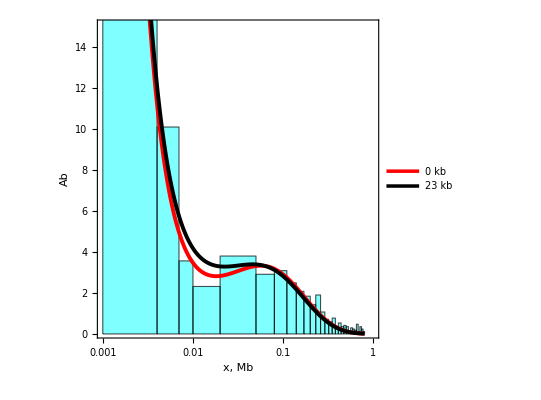

```mathematica
Show[Histogram[{Flatten[Exp1]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,15}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Ab"}],Plot[{(AbF/.β->100/.x->xi/0.431)*8+0.0005*xi^(-1.8),(AbF/.β->20/.x->xi/0.431)*7.5+0.0005*xi^(-1.8)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","43 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

```mathematica
D[(AbF/.β->18/.x->xi/0.431)*8+0.0025*xi^(-1.5),xi]
```

0.0202061 (26.3054 (-47.064 ⅇ^(-26.7069 xi)-0.588706 ⅇ^(-21.1451 xi)-9.58565 ⅇ^(-8.05314 xi))+46.648 (2.63935 ⅇ^(-26.7069 xi)+0.567052 ⅇ^(-21.1451 xi)-1.01182 ⅇ^(-8.05314 xi))+2767.16 (3.77239 ⅇ^(-26.7069 xi)-0.457797 ⅇ^(-21.1451 xi)-0.963165 ⅇ^(-8.05314 xi)))-0.00375/xi^2.5

```mathematica
N[431/18]
```

23.9444

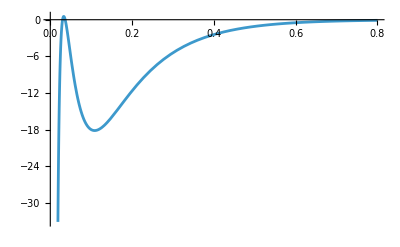

```mathematica
Plot[0.020206102242877347 (26.305376178417365 (-47.06397686177056 ⅇ^(-26.70693086744566 xi)-0.5887064186797721 ⅇ^(-21.145076043767407 xi)-9.585649027198423 ⅇ^(-8.05313883572143 xi))+46.64795231233706 (2.6393468031365925 ⅇ^(-26.70693086744566 xi)+0.5670518041521583 ⅇ^(-21.145076043767407 xi)-1.0118244680910553 ⅇ^(-8.05313883572143 xi))+2767.15798244389 (3.7723947707615038 ⅇ^(-26.70693086744566 xi)-0.4577968972142196 ⅇ^(-21.145076043767407 xi)-0.9631654177367832 ⅇ^(-8.05313883572143 xi)))-0.00375/xi^2.5,{xi,0.0006,0.8}]
```

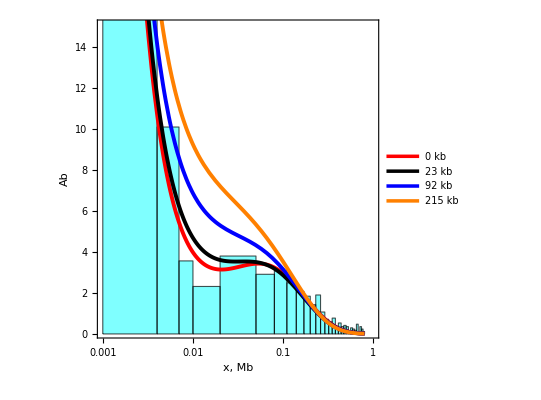

```mathematica
Show[Histogram[{Flatten[Exp1]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,15}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Ab"}],Plot[{(AbF/.β->100/.x->xi/0.431)*8+0.0025*xi^(-1.5),(AbF/.β->20/.x->xi/0.431)*7.5+0.0025*xi^(-1.5),(AbF/.β->5/.x->xi/0.431)*7.5+0.0025*xi^(-1.5),(AbF/.β->2/.x->xi/0.431)*7.5+0.0025*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Orange,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","92 kb","215 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

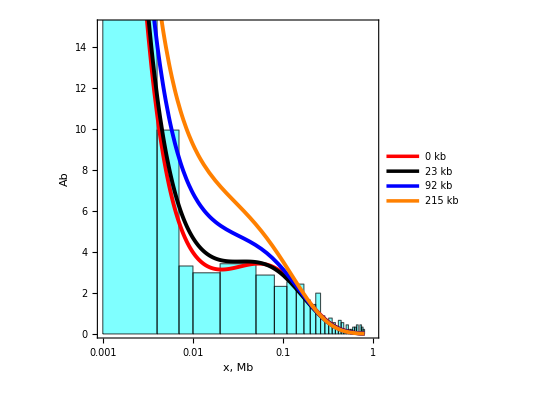

```mathematica
Show[Histogram[{Flatten[ExpPP]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,15}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Ab"}],Plot[{(AbF/.β->100/.x->xi/0.431)*8+0.0025*xi^(-1.5),(AbF/.β->20/.x->xi/0.431)*7.5+0.0025*xi^(-1.5),(AbF/.β->5/.x->xi/0.431)*7.5+0.0025*xi^(-1.5),(AbF/.β->2/.x->xi/0.431)*7.5+0.0025*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Orange,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","92 kb","215 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

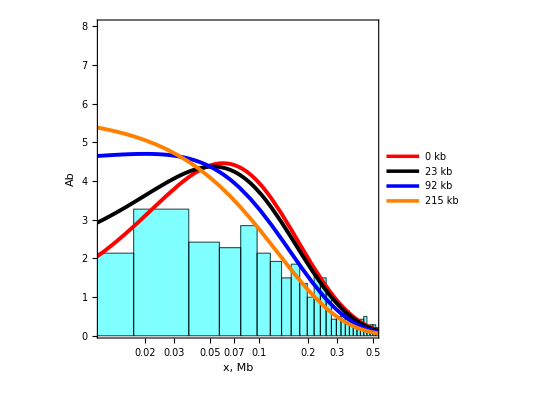

```mathematica
Show[Histogram[{Flatten[Exp1]},{bins3},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.011,0.5},{0.1,8}},FrameTicks->{{All,None},{{0.001,0.01,0.02,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Ab"}],Plot[{(AbF/.β->100/.x->xi/0.431)*11,(AbF/.β->20/.x->xi/0.431)*10,(AbF/.β->5/.x->xi/0.431)*8,(AbF/.β->2/.x->xi/0.431)*6},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Orange,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","92 kb","215 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

```mathematica
bins3=Join[Range[0.01,10,0.02]];
```

```mathematica
bins4=Join[Range[0.01,10,0.025]];
```

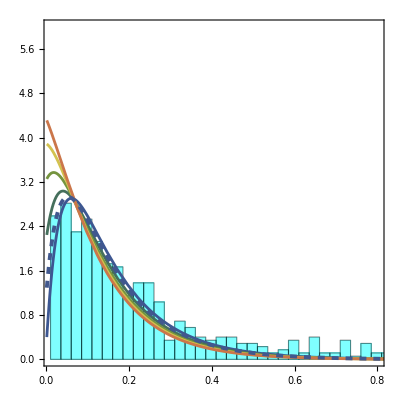

```mathematica
gAbexp=Show[Histogram[Flatten[Exp1],{bins4},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0.01,0.8},{0,6}},FrameTicks->{{All,None},{All,None}}],Plot[{Evaluate[Table[0.6/0.431Abnorm[xi/0.431,1/lsw],{lsw,0.01,lswmax,lswstep}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}]],Plot[{Evaluate[0.6/0.431Abnorm[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][1-0.05/lswmax],Dashing[Small],Thickness[0.007]],ImageSize->300]
]
```

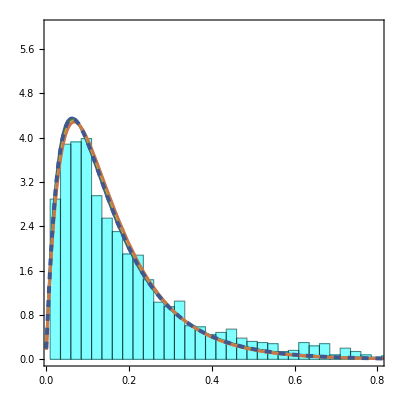

```mathematica
gAbbexp=Show[Histogram[Flatten[ExpPM],{bins4},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0.011,0.8},{0,6}},FrameTicks->{{All,None},{All,None}}],Plot[{Evaluate[Table[0.9/0.431AbbNorm[xi/0.431,1/lsw],{lsw,0.01,lswmax,lswstep}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}]],Plot[{Evaluate[0.9/0.431AbbNorm[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][1-0.05/lswmax],Dashing[Small],Thickness[0.007]],ImageSize->300]
]
```

```mathematica
bins4=Join[Range[0.008,0.8,0.015]];
```

```mathematica
bins2=Join[Range[0.001,0.01,0.003],Range[0.02,10,0.03]];
```

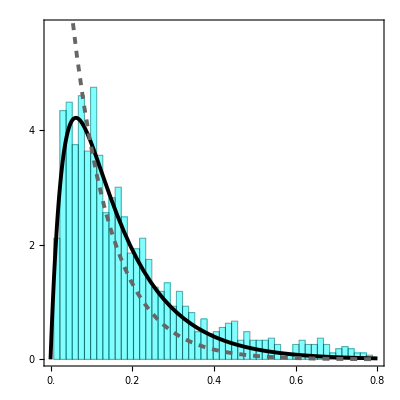

```mathematica
Show[Histogram[Flatten[ExpPM],{bins4},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0,0.8},{0,5.8}},FrameTicks->{{Range[0,7,2],None},(*left,right*){Range[0,0.8,0.2],None}        (*bottom,top*)}],Plot[{modelCTCF/.lp->0.431/.α->1.2/.γ->3.7/.γo->4/.Ai->18/.x->xi,1/lOne*Exp[-xi/lOne]},{xi,0,0.8},PlotStyle->{Directive[Black,Thickness[0.007]],Directive[RGBColor[0.4,0.4,0.4],Thickness[0.007],Dashed]}]]
```

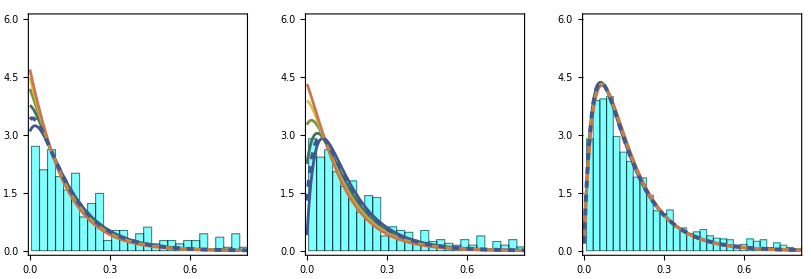

```mathematica
GraphicsRow[{gA00exp,gAbexp,gAbbexp}]
```

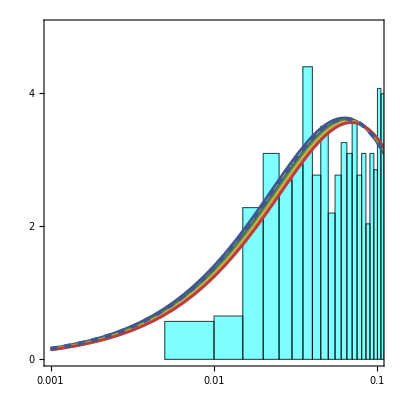

```mathematica
Show[Histogram[{Flatten[ExpPM]},{0.005},"PDF",AspectRatio->1,PlotRange->{{0.001,0.1},{0,5}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[24],
FrameTicks->{{Range[0,7,2],None},(*left,right*){{0.01,0.1},None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},ScalingFunctions->{"Log",None}],Plot[{Evaluate[Table[0.75/0.431AbbNorm[xi/0.431,1/lsw],{lsw,0.01,lswmax,lswstep}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],ScalingFunctions->{"Log",None}],Plot[{Evaluate[0.75/0.431AbbNorm[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][1-0.05/lswmax],Dashing[Small],Thickness[0.007]],ScalingFunctions->{"Log",None}]]
```

```mathematica
Table[lsw,{lsw,0.01,lswmax,lswstep}]
```

{0.01,0.11,0.21,0.31,0.41,0.51}

```mathematica
{0.0001,0.1,0.25,0.5}
```

```mathematica
N[20/431]
```

0.0464037

```mathematica
lswT={0.0001,0.046,0.0,0.1,0.25,0.5}
```

{0.0001,0.046,0.,0.1,0.25,0.5}

```mathematica
AF[xi/0.431,1/lsw]/.lsw->lswT
```

AF[2.32019 xi,{10000.,10.,4.,2.}]

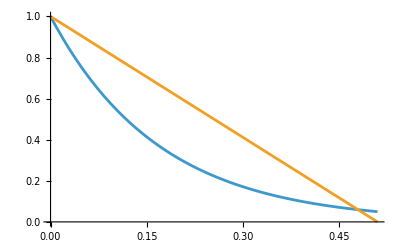

```mathematica
Plot[{Exp[-x*3/lswmax],1-x/lswmax},{x,0,lswmax}]
```

```mathematica
Table[lswT[[i]]*0.431,{i,1,Length[lswT]}]
```

{0.0000431,0.05172,0.10775,0.2155}

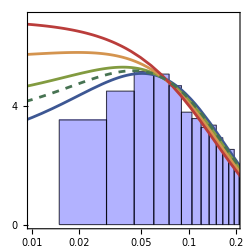

```mathematica
Show[Histogram[{GMrad21},{0.015},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0.01,0.2},{0,7}},FrameTicks->{{Range[0,4,4],None},(*left,right*){Range[0.,0.4,0.4],None}        (*bottom,top*)},ScalingFunctions->{"Log",None}],Plot[{Evaluate[Table[1.05/0.431AF[xi/0.431,1/lswT[[i]]],{i,1,Length[lswT]}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*lswT[[i]]/lswmax]]],{i,1,Length[lswT]}],ScalingFunctions->{"Log",None}],Plot[{Evaluate[1.05/0.431AF[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*0.05/lswmax]],Dashing[Small]],ScalingFunctions->{"Log",None}],ImageSize->250]
```

```mathematica
Min[GMrad21]
```

0.015749

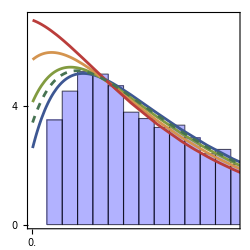

```mathematica
Show[Histogram[{GMrad21},{0.015},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0,0.2},{0,7}},FrameTicks->{{Range[0,4,4],None},(*left,right*){Range[0.,0.4,0.4],None}        (*bottom,top*)}],Plot[{Evaluate[Table[1.05/0.431AF[xi/0.431,1/lswT[[i]]],{i,1,Length[lswT]}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*lswT[[i]]/lswmax]]],{i,1,Length[lswT]}]],Plot[{Evaluate[1.05/0.431AF[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*0.05/lswmax]],Dashing[Small]]],ImageSize->250]
```

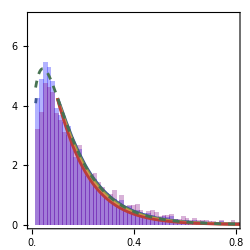

```mathematica
(*1. Normalization settings*)Clear[histData,histMax,pkNormAF,pkPDF];

lp=0.431;
lcut=0.0158;
binWidth=0.015;

(*Experimental data above cutoff*)
histData=(Select[Flatten[{#}],NumericQ[#]&&TrueQ[#>=lcut]&]&)/@{GMrep1,GMrep2};

(*Include all observed lengths in normalization*)
histMax=lcut+binWidth (Ceiling[(Max[Flatten[histData]]-lcut)/binWidth]+1);

(*Normalization for each theoretical curve*)
pkNormAF[sw_?NumericQ]:=pkNormAF[sw]=NIntegrate[AF[u,1./sw],{u,lcut/lp,Infinity},AccuracyGoal->8,MaxRecursion->20];

(*PDF normalized above the experimental cutoff*)
pkPDF[x_,sw_?NumericQ]:=AF[x/lp,1./sw]/(lp pkNormAF[sw]);

(*Precompute normalization constants*)
pkNormAF/@Join[lswT,{0.05}];

(*2. Figure*)
Show[Histogram[histData,{lcut,histMax,binWidth},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]],Directive[RGBColor[0.5,0,0.5],Opacity[0.3],EdgeForm[Black]]}],Plot[Evaluate[Table[pkPDF[xi,lswT[[i]]],{i,1,Length[lswT]}]],{xi,lcut,1.2},PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3 lswT[[i]]/lswmax]]],{i,1,Length[lswT]}]],Plot[Evaluate[pkPDF[xi,0.05]],{xi,lcut,1.2},PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3 0.05/lswmax]],Dashing[Small]]],PlotRange->{{0,0.8},{0,7}},PlotRangePadding->None,Frame->True,Axes->False,FrameTicks->{{Range[0,8,2],None},{Range[0.,0.8,0.2],None}},FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],AspectRatio->1,ImageSize->250]
```

```mathematica
Plot[{modelRad/.lp->0.431/.α->1.2/.γ->3.1/.γo->4/.Ai->2.48/.x->xi,1/0.144*Exp[-xi/0.144]},{xi,0,0.8},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[RGBColor[0.5,0.5,0.5],Thickness[0.004]]}]
```

```mathematica
lOne=lp/(1+(γ/2+γo/(1+α)))/.α->1.2/.γ->3.2/.γo->4
```

0.0975514

```mathematica
lTwo=lp/(1+(γ/2+γo/(1+α))/2)/.α->1.2/.γ->3.7/.γo->4
```

0.152077

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::inumr: The integrand AF[u,ComplexInfinity] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.0366589}}.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

NIntegrate::inumr: The integrand AF[u,ComplexInfinity] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.0366589}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

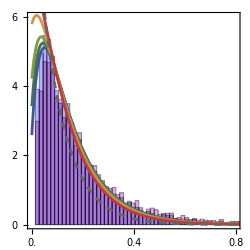

```mathematica
Show[Histogram[{GMrep1,GMrep2},{0.015},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]],Directive[RGBColor[0.5,0,0.5],Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0,0.8},{0,6}},FrameTicks->{{Range[0,6,2],None},(*left,right*){Range[0.,0.8,0.2],None}        (*bottom,top*)}],Plot[{Evaluate[Table[pkPDF[xi,lswT[[i]]],{i,1,Length[lswT]}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*lswT[[i]]/lswmax]]],{i,1,Length[lswT]}]],Plot[{1/lOne*Exp[-xi/lOne]},{xi,0.001,1.2},PlotRange->All,PlotStyle->{Directive[RGBColor[0.4,0.4,0.4],Dashed]},ImageSize->250]]
```

```mathematica
bins4=Join[Range[0.008,0.8,0.015]];
```

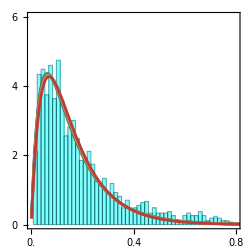

```mathematica
Show[Histogram[{Flatten[ExpPM]},{bins4},"PDF",AspectRatio->1,PlotRange->{{0.001,0.8},{0,6}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],FrameTicks->{{Range[0,6,2],None},(*left,right*){Range[0.,0.8,0.2],None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]}],Plot[{Evaluate[Table[0.9/0.431AbbNorm[xi/0.431,1/lswT[[i]]],{i,1,Length[lswT]}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*lswT[[i]]/lswmax]]],{i,1,Length[lswT]}]],ImageSize->250]
```

```mathematica
Exp[-3*x/lswmax]
```

ⅇ^(-5.88235 x)

0.232019

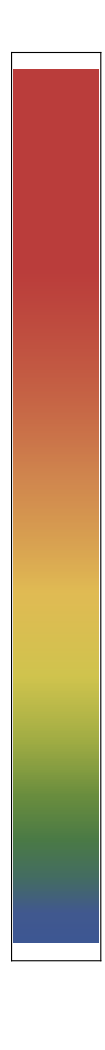

```mathematica
ClearAll[swColor,legend];

(*The same color mapping as in the main plot*)
swColor[ell_?NumericQ]:=ColorData[{"DarkRainbow","Reverse"}][Exp[-3.0 ell/lswmax]];
0.1/0.431
(*Number of strips in the color scale*)
nColors=300;

nColors=500;

legend=Graphics[Raster[Table[{List@@swColor[(i-0.5) lswmax/nColors]},{i,1,nColors}],{{0,0},{1,lswmax}}],PlotRange->{{0,1},{0,lswmax}},PlotRangePadding->None,Frame->True,FrameTicks->{{None,Table[{v,Round[v*431]},{v,0,0.5,0.05/0.431}]},{None,None}},FrameStyle->Directive[24,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[20,FontFamily->"CMU Serif",Black],ImagePadding->{{3,48},{5,5}},AspectRatio->10,ImageSize->{105,350}];


legend
```

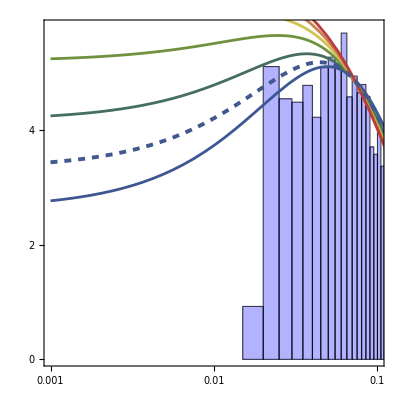

```mathematica
Show[Histogram[{GMrad21},{0.005},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[24],ChartStyle->{Directive[Blue,Opacity[0.3],EdgeForm[Black]]},PlotRange->{{0.001,0.1},{0,5.8}},FrameTicks->{{Range[0,7,2],None},(*left,right*){{0.01,0.1},None}        (*bottom,top*)},ScalingFunctions->{"Log",None}],Plot[{Evaluate[Table[1.05/0.431AF[xi/0.431,1/lsw],{lsw,0.01,lswmax,lswstep}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],ScalingFunctions->{"Log",None}],Plot[{Evaluate[1.05/0.431AF[xi/0.431,20]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Directive[ColorData[{"DarkRainbow","Reverse"}][1-0.05/lswmax],Dashing[Small],Thickness[0.007]],ScalingFunctions->{"Log",None}]]
```

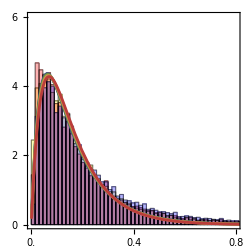

```mathematica
Show[Histogram[{Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths],Flatten[k562LoopLengths],Flatten[helaLoopLengths],Flatten[gm12878LoopLengths]},{0.015},"PDF",AspectRatio->1,PlotRange->{{0.001,0.8},{0,6}},Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],FrameTicks->{{Range[0,6,2],None},(*left,right*){Range[0.,0.8,0.2],None}        (*bottom,top*)},
ChartStyle->{Directive[RGBColor[1,1,0],Opacity[0.3]],Directive[RGBColor[1,0,0],Opacity[0.3]],Directive[RGBColor[0,0,1],Opacity[0.3]],Directive[RGBColor[0,1,0],Opacity[0]],Directive[RGBColor[0.5,0.5,1],Opacity[0]],Directive[RGBColor[1,0.5,0.5],Opacity[0]]}],Plot[{Evaluate[Table[0.9/0.431AbbNorm[xi/0.431,1/lswT[[i]]],{i,1,Length[lswT]}]]},{xi,0.001,1.2},PlotRange->All,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][Exp[-3*lswT[[i]]/lswmax]]],{i,1,Length[lswT]}]],ImageSize->250]
```

```mathematica
ki=5;
k2=0.007;
```

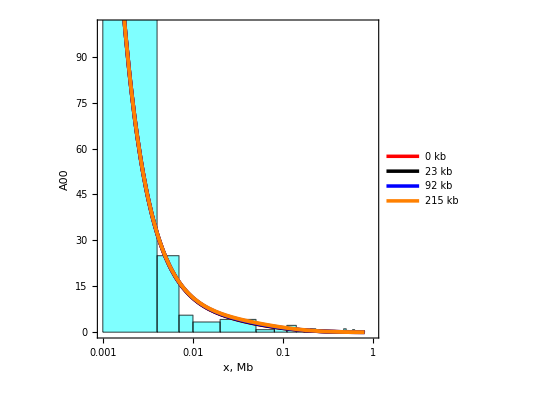

```mathematica
Show[Histogram[{Flatten[ExpMP]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,100}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","A00"}],Plot[{(A11F/.β->100/.x->xi/0.431)*ki+k2*xi^(-1.5),(A11F/.β->20/.x->xi/0.431)*ki+k2*xi^(-1.5),(A11F/.β->5/.x->xi/0.431)*ki+k2*xi^(-1.5),(A11F/.β->2/.x->xi/0.431)*1ki+k2*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Orange,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","92 kb","215 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

```mathematica
ki=20;
k2=0.0003;
```

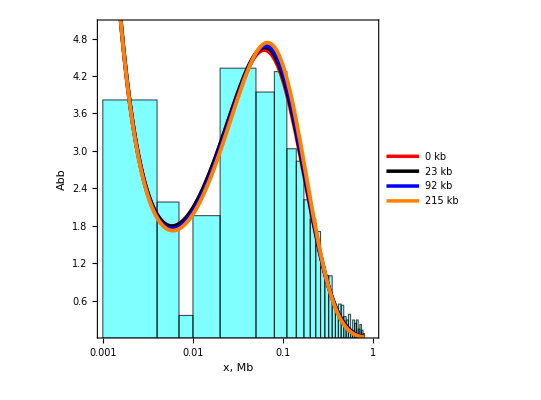

```mathematica
Show[Histogram[{Flatten[ExpPM]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,5}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Abb"}],Plot[{(AbbF/.β->100/.x->xi/0.431)*ki+k2*xi^(-1.5),(AbbF/.β->20/.x->xi/0.431)*1.08ki+k2*xi^(-1.5),(AbbF/.β->5/.x->xi/0.431)*1.35ki+k2*xi^(-1.5),(AbbF/.β->2/.x->xi/0.431)*1.9ki+k2*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]],Directive[Orange,Thickness[0.007]]},PlotLegends->{"0 kb","23 kb","92 kb","215 kb"},Exclusions->None,ScalingFunctions->{"Log",None}]]
```

```mathematica
bins2=Join[Range[0.001,0.01,0.003],Range[0.02,0.8,0.03]];
```

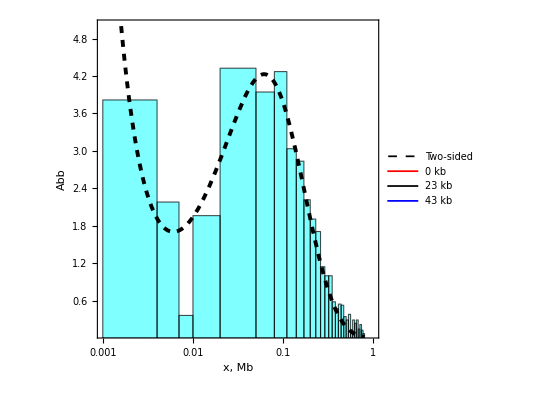

```mathematica
Show[Histogram[{Flatten[ExpPM]},{bins2},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]],Directive[RGBColor[1,0,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.1,5}},FrameTicks->{{All,None},{{0.0006,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","Abb"}],Plot[{Evaluate[modelCTCF/. Ai->18/. lp->0.431/. α->1.2/.
γ->3.7/. γo->4/. x->xi]+0.0003*xi^(-1.5), 4.3PhiBBContact[xi/0.431,3.7,0.05,0.001]+0.0003*xi^(-1.5),4.3PhiBBContact[xi/0.431,3.7,0.05,0.001]+0.0003*xi^(-1.5),4.3PhiBBContact[xi/0.431,3.7,0.1,0.001]+0.0003*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->{0,5},PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[Red,Thickness[0.007]],Directive[Black,Thickness[0.007]],Directive[Blue,Thickness[0.007]]},ScalingFunctions->{"Log",None},PlotLegends->{"Two-sided","0 kb","23 kb","43 kb"}]]
```

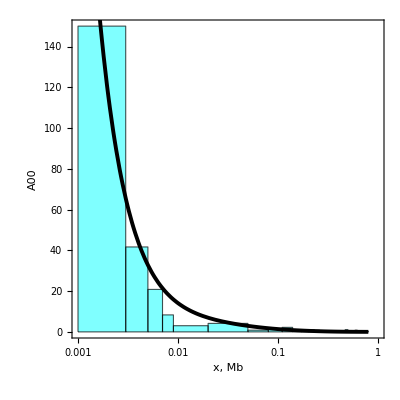

```mathematica
Show[Histogram[Flatten[ExpMP],{bins},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0.001,1},{0.,150}},FrameTicks->{{All,None},{{0.0006,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None},FrameLabel->{"x, Mb","A00"}],Plot[{Evaluate[modelA11/. Ai->5/. lp->0.431/. α->1.2/.
γ->3.7/. γo->4/. x->xi]+0.01*xi^(-1.5)},{xi,0.0006,0.8},PlotRange->All,PlotStyle->{Directive[Black,Thickness[0.007]]},ScalingFunctions->{"Log",None}]]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[simD2].

Histogram::ldata: Flatten[simD2] is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in ….

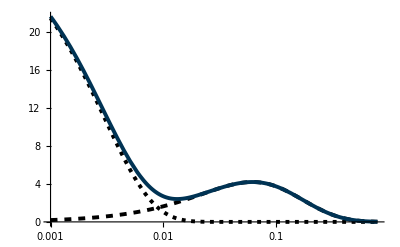
Show[Histogram[Flatten[simD2],{0.003},PDF,AspectRatio→1,Frame→True,FrameStyle→Directive[20,FontFamily→Times,GrayLevel[0]],FrameTicksStyle→Directive[20],ChartStyle→{Directive[RGBColor[0, 1, 1],Opacity[0.5]]},PlotRange→{{0.003,1},{0,20}},FrameTicks→{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions→{Log,None}],-Graphics-]

```mathematica
Show[Histogram[Flatten[simD2],{0.003},"PDF",AspectRatio->1,Frame->True,FrameStyle->Directive[20,FontFamily->"Times",Black],FrameTicksStyle->Directive[20],ChartStyle->{Directive[RGBColor[0,1,1],Opacity[0.5]]},PlotRange->{{0.003,1},{0,20}},FrameTicks->{{All,None},{{0.001,0.01,0.1,0.5},None}},ScalingFunctions->{"Log",None}],Plot[{Evaluate[modelCTCF/. Ai->18/. lp->0.431/. α->1.2/.
γ->3.7/. γo->4/. x->xi],Exp[-xi/0.003]*30,Evaluate[modelCTCF/. Ai->18/. lp->0.431/. α->1.2/.
γ->3.7/. γo->4/. x->xi]+Exp[-xi/0.003]*30},{xi,0.001,0.8},PlotRange->All,PlotStyle->{Directive[Black,Dashed,Thickness[0.007]],Directive[Black,Dashing[{0.007,0.01}],Thickness[0.007]],Directive[RGBColor[0.,0.2,0.33],Thickness[0.007]]},ScalingFunctions->{"Log",None}]]
```

## Fig 2 efgh

```mathematica
lswmax=0.51;
lswstep=0.1;
```

```mathematica
legend=DensityPlot[y,{x,0,1},{y,0,1},AspectRatio->10,FrameTicks->{{None,Table[{γ/lswmax,γ},{γ,0,lswmax,lswstep}]},{None,None}},ColorFunction->"DarkRainbow",FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[18,FontFamily->"CMU Serif",Black],RotateLabel->False,ImageSize->70,PlotRangePadding->None]
```

-Graphics-

```mathematica
legend2=DensityPlot[y,{x,0,1},{y,0,1},AspectRatio->10,FrameTicks->{{None,Table[{γ/lswmax,γ*0.4},{γ,0,lswmax,lswstep}]},{None,None}},ColorFunction->"DarkRainbow",FrameStyle->Directive[18,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[18,FontFamily->"CMU Serif",Black],RotateLabel->False,ImageSize->60,PlotRangePadding->None]
```

-Graphics-

## TSW = 0.05

```mathematica
dataA00=Flatten[(Import["C:\\петли\\численное моделирование\\drive-download-20261114T183859Z-1-001\\A11_collision_pc1_sv2_root1_m3_n100000_nch20_dc0.001_size0.015_tsw0.05_g2.7_gb4_alpha1.2_run3c2166b4.csv","CSV"][[2;;]])];
```

```mathematica
dataA=Flatten[(Import["C:\\петли\\численное моделирование\\drive-download-20261114T183859Z-1-001\\A_collision_pc1_sv2_root1_m3_n100000_nch20_dc0.001_size0.015_tsw0.05_g2.7_gb4_alpha1.2_run3c2166b4.csv","CSV"][[2;;]])];
```

```mathematica
dataAb=Join[Flatten[(Import["C:\\петли\\численное моделирование\\drive-download-20261114T183859Z-1-001\\Ab1_collision_pc1_sv2_root1_m3_n100000_nch20_dc0.001_size0.015_tsw0.05_g2.7_gb4_alpha1.2_run3c2166b4.csv","CSV"][[2;;]])],Flatten[(Import["C:\\петли\\численное моделирование\\drive-download-20261114T183859Z-1-001\\Abp_collision_pc1_sv2_root1_m3_n100000_nch20_dc0.001_size0.015_tsw0.05_g2.7_gb4_alpha1.2_run3c2166b4.csv","CSV"][[2;;]])]];
```

```mathematica
dataAbb=Flatten[(Import["C:\\петли\\численное моделирование\\drive-download-20261114T183859Z-1-001\\Abb_collision_pc1_sv2_root1_m3_n100000_nch20_dc0.001_size0.015_tsw0.05_g2.7_gb4_alpha1.2_run3c2166b4.csv","CSV"][[2;;]])];
```

## TSW = 0.2

```mathematica
dataA0002=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_0.2\\A11_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.2_g2.7_gb4_alpha1.2_runce4cdb49.csv","CSV"][[2;;]])];
```

```mathematica
dataA02=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_0.2\\A_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.2_g2.7_gb4_alpha1.2_runce4cdb49.csv","CSV"][[2;;]])];
```

```mathematica
dataAb02=Join[Flatten[(Import["C:\\петли\\численное моделирование\\tsw_0.2\\Ab1_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.2_g2.7_gb4_alpha1.2_runce4cdb49.csv","CSV"][[2;;]])],Flatten[(Import["C:\\петли\\численное моделирование\\tsw_0.2\\Abp_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.2_g2.7_gb4_alpha1.2_runce4cdb49.csv","CSV"][[2;;]])]];
```

```mathematica
dataAbb02=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_0.2\\A_bb_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.2_g2.7_gb4_alpha1.2_runce4cdb49.csv","CSV"][[2;;]])];
```

## TSW = 0.5

```mathematica
dataA0005=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_05\\A11_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.5_g2.7_gb4_alpha1.2_runcc67cd47.csv","CSV"][[2;;]])];
```

```mathematica
dataA05=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_05\\A_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.5_g2.7_gb4_alpha1.2_runcc67cd47.csv","CSV"][[2;;]])];
```

```mathematica
dataAb05=Join[Flatten[(Import["C:\\петли\\численное моделирование\\tsw_05\\Ab1_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.5_g2.7_gb4_alpha1.2_runcc67cd47.csv","CSV"][[2;;]])],Flatten[(Import["C:\\петли\\численное моделирование\\tsw_05\\Abp_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.5_g2.7_gb4_alpha1.2_runcc67cd47.csv","CSV"][[2;;]])]];
```

```mathematica
dataAbb05=Flatten[(Import["C:\\петли\\численное моделирование\\tsw_05\\Abb_collision_pc1_sv2_m3_n100000_nch50_dc0.0015_size0.015_tsw0.5_g2.7_gb4_alpha1.2_runcc67cd47.csv","CSV"][[2;;]])];
```

## GRAPHS

```mathematica
bins2=Join[Range[0,10,0.05]];
```

```mathematica
FSize=20;
FTicksSize=16;
```

```mathematica
gA1=Show[Histogram[Flatten[dataA],100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AF[xi,20]],{xi,0,1},PlotRange->{0,3},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[AF[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,0,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250];
gA1v1=Show[Histogram[Flatten[dataA],100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AF[xi,20]],{xi,0,1},PlotRange->{0,3},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gA102=Show[Histogram[Flatten[dataA02],100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AF[xi,5]],{xi,0,1},PlotRange->{0,3},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gA105=Show[Histogram[Flatten[dataA05],100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AF[xi,2]],{xi,0,1},PlotRange->{0,3},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
```

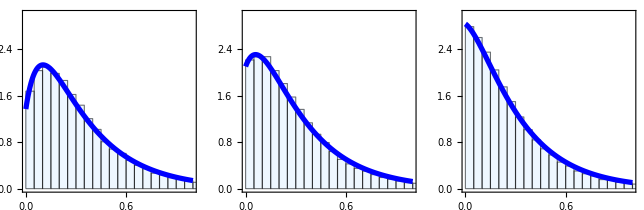

```mathematica
GraphicsRow[{gA1v1,gA102,gA105}]
```

```mathematica
gAbb=Show[Histogram[Flatten[dataAbb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AbbNorm[xi,20]],{xi,0,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[AbbNorm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,0,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250];
gAbbv1=Show[Histogram[Flatten[dataAbb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AbbNorm[xi,20]],{xi,0,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gAbb02=Show[Histogram[Flatten[dataAbb02],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AbbNorm[xi,5]],{xi,0,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gAbb05=Show[Histogram[Flatten[dataAbb05],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AbbNorm[xi,2]],{xi,0,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
```

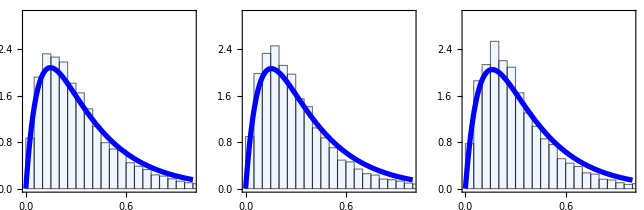

```mathematica
GraphicsRow[{gAbbv1,gAbb02,gAbb05}]
```

```mathematica
gA00=Show[Histogram[Flatten[dataA00],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,8}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[A11norm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[A11norm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,-0.1,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250];
gA00v1=Show[Histogram[Flatten[dataA00],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,8}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[A11norm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gA0002=Show[Histogram[Flatten[dataA0002],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,8}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[A11norm[xi,5]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gA0005=Show[Histogram[Flatten[dataA0005],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,8}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[A11norm[xi,2]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
```

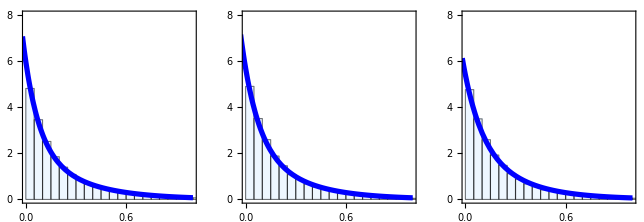

```mathematica
GraphicsRow[{gA00v1,gA0002,gA0005}]
```

```mathematica
gAb=Show[Histogram[Flatten[dataAb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,4}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Abnorm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[Abnorm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,-0.1,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250];
```

```mathematica
gAbv1=Show[Histogram[Flatten[dataAb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,4}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Abnorm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gAb02=Show[Histogram[Flatten[dataAb02],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,4}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Abnorm[xi,5]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
gAb05=Show[Histogram[Flatten[dataAb05],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,4}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Abnorm[xi,2]],{xi,-0.1,1},Frame->True,PlotStyle->{Blue,Thickness[0.015]},AspectRatio->1],ImageSize->250];
```

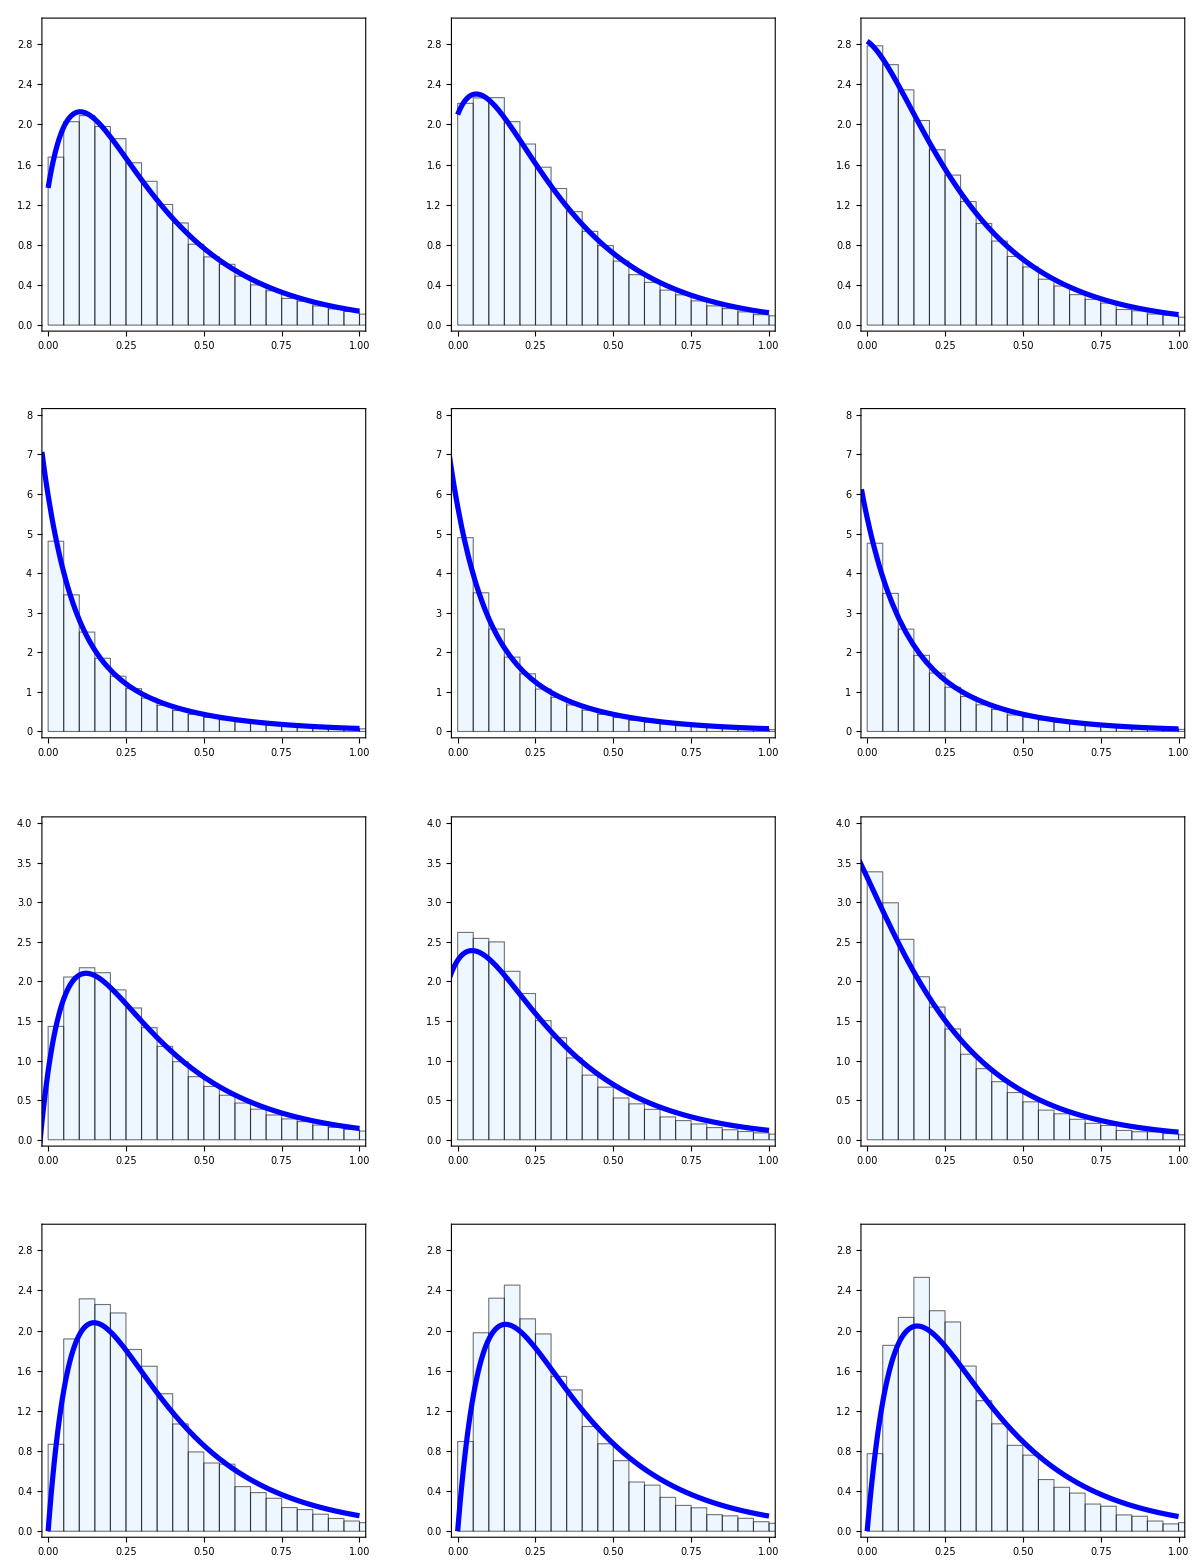

```mathematica
Show[GraphicsGrid[{{gA1v1,gA102,gA105},{gA00v1,gA0002,gA0005},{gAbv1,gAb02,gAb05},{gAbbv1,gAbb02,gAbb05}}]]
```

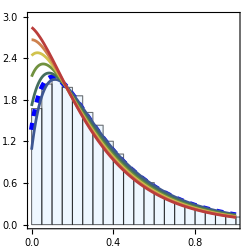

```mathematica
gA1=Show[Histogram[Flatten[dataA],100,"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AF[xi,20]],{xi,0,1},PlotRange->{0,3},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[AF[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,0,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250]
```

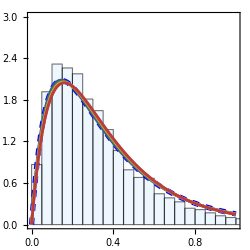

```mathematica
gAbb=Show[Histogram[Flatten[dataAbb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,3}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[AbbNorm[xi,20]],{xi,0,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[AbbNorm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,0,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250]
```

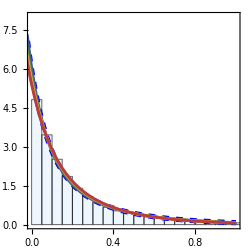

```mathematica
gA00=Show[Histogram[Flatten[dataA00],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,8}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[A11norm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[A11norm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,-0.1,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250]
```

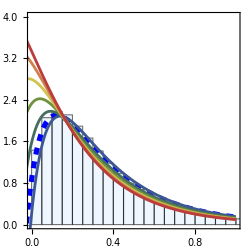

```mathematica
gAb=Show[Histogram[Flatten[dataAb],{bins2},"PDF",ChartStyle->Directive[LightBlue,Opacity[0.5],ChartBaseStyle->EdgeForm[Gray]],Frame->True,FrameStyle->Directive[FSize,FontFamily->"CMU Serif",Black],FrameTicksStyle->Directive[FTicksSize,FontFamily->"CMU Serif",Black],AspectRatio->1,PlotRange->{{0.,1},{0,4}},FrameLabel->{{None,None},{None,None}}],
Plot[Evaluate[Abnorm[xi,20]],{xi,-0.1,1},Frame->True,PlotStyle->{Dashing[Small],Blue,Thickness[0.015]},AspectRatio->1],Plot[Evaluate[Table[Abnorm[xi,1/lsw],{lsw,0.01,lswmax,lswstep}]],{xi,-0.1,1},Frame->True,PlotStyle->Table[Directive[ColorData[{"DarkRainbow","Reverse"}][1-lsw/lswmax]],{lsw,0.01,lswmax,lswstep}],AspectRatio->1],ImageSize->250]
```

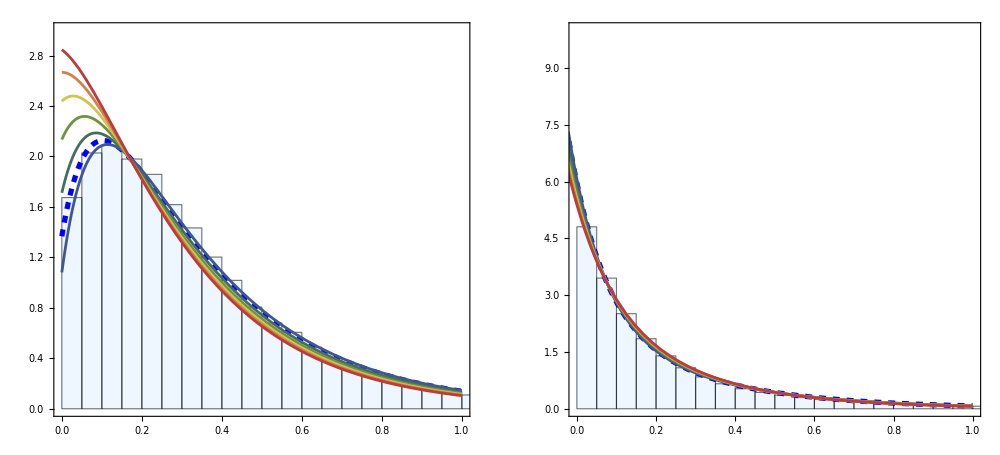

```mathematica
GraphicsRow[{gA1,gA00,legend}]
```

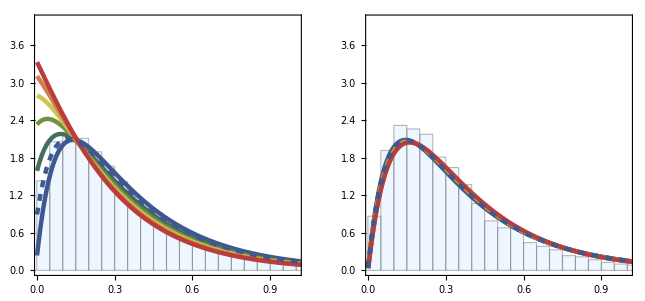

```mathematica
GraphicsRow[{gAb,gAbb,legend}]
```

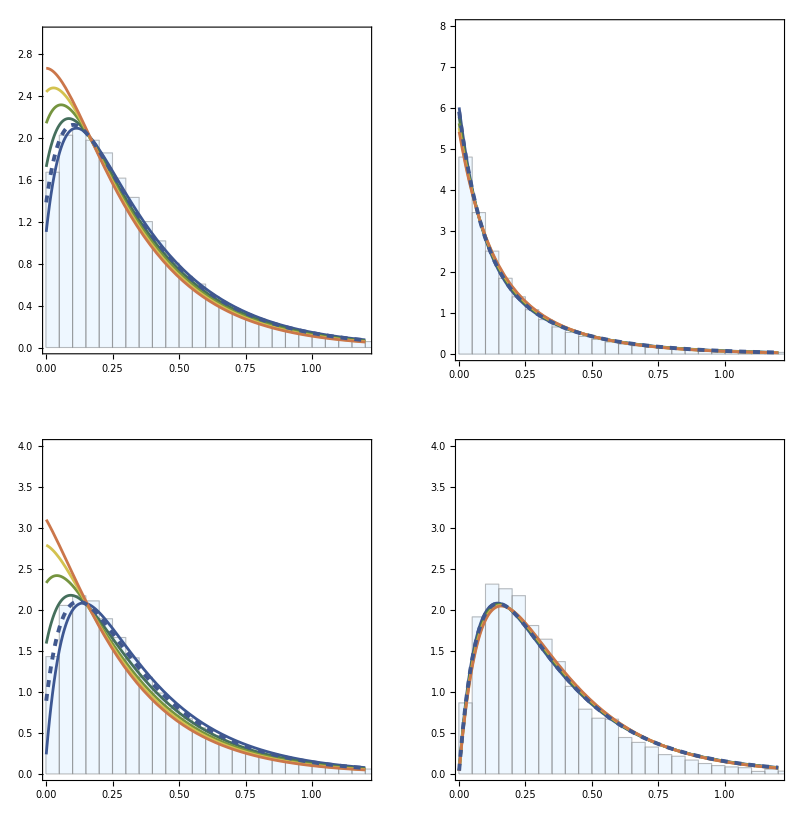

```mathematica
GraphicsGrid[{{gA1,gA00},{gAb,gAbb}}]
```

# Unified fitting of ChIA-PET and HiChIP loop-length distributions

```mathematica
(* modelRad and modelCTCF must be defined before this code is run.
   Expected model symbols: x, Ai, α, γ, γo, lp. *)

(* ------------------------------------------------------------------ *)
(* 1. Input files and dataset settings                                 *)
(* ------------------------------------------------------------------ *)

baseDir = NotebookDirectory[];

(* Output directory of chia_pet_unified_pipeline_no_pet_filter.py *)
chiaPetDir = "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\chia_pet_results\\loop_length";

(* The separate HiChIP table *)
hiChipFile ="C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\hichip_results\\CTCF_HICHIP.csv";

binKb = 10.;

ClearAll[findOne];

findOne::files = "Pattern `1` matched `2` files: `3`.";

findOne[directory_, pattern_] := Module[
  {files = FileNames[pattern, directory]},

  If[Length[files] != 1,
    Message[findOne::files, pattern, Length[files], files];
    Abort[]
  ];

  First[files]
];

(* These are the six combined PET-expanded files generated by Python.
   The *.csv* suffix accepts both .csv and .csv.gz. *)
chiaPetFiles = <|
  "RadK562" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\K562rad21.csv",

  "RadGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\GMrad21.csv",

  "CTCFK562" -> "C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\k562LoopLengthsCTCF.csv",

  "CTCFGM" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\gm12878LoopLengthsCTCF.csv",

  "CTCFHeLa" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\helaLoopLengthsCTCF.csv",

  "CTCFMCF7" ->"C:\\петли\\ЭКСПЕРИМЕНТЫ\\Обработка данны\\new\\mcf7LoopLengthsCTCF.csv"
|>;

If[!FileExistsQ[hiChipFile],
  Print["HiChIP file was not found: ", hiChipFile];
  Abort[]
];

(* The order is intentional:
   columns 5-11  = fitted amplitudes;
   columns 12-18 = RMSE, matching the previous tbls structure;
   columns 19-25 = nRMSE. *)
datasetOrder = {
  "RadK562",
  "RadGM",
  "CTCFK562Hi",
  "CTCFK562",
  "CTCFGM",
  "CTCFHeLa",
  "CTCFMCF7"
};

specs = <|
  "RadK562" -> <|
    "File" -> chiaPetFiles["RadK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30.,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "RadGM" -> <|
    "File" -> chiaPetFiles["RadGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelRad,
    "MinKb" -> 30,
    "MaxKb" -> 800.,
    "XScale" -> 1.,
    "LpScale" -> 1.,
    "A0" -> 0.003
  |>,

  "CTCFK562Hi" -> <|
    "File" -> hiChipFile,
    "Column" -> "interaction_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 30.,              (* remove HiChIP short-range contacts *)
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,       (* lp grid is in kb; model uses Mb *)
    "A0" -> 3.
  |>,

  "CTCFK562" -> <|
    "File" -> chiaPetFiles["CTCFK562"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFGM" -> <|
    "File" -> chiaPetFiles["CTCFGM"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFHeLa" -> <|
    "File" -> chiaPetFiles["CTCFHeLa"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>,

  "CTCFMCF7" -> <|
    "File" -> chiaPetFiles["CTCFMCF7"],
    "Column" -> "loop_length_kb",
    "Model" -> modelCTCF,
    "MinKb" -> 10.,
    "MaxKb" -> 600.,
    "XScale" -> 1.,        (* kb -> Mb *)
    "LpScale" -> 1.,  
    "A0" -> 3.
  |>
|>;
```

```mathematica
(* ------------------------------------------------------------------ *)
(* 2. Import and construction of uniformly binned PDFs                 *)
(* ------------------------------------------------------------------ *)

ClearAll[importCSV, toNumber, readNumericColumn, makePDFData];

(* Import works directly for ordinary CSV. For .csv.gz, Mathematica usually
   detects compression automatically; the fallback explicitly decompresses
   the file and parses the resulting CSV string. *)
importCSV[file_] := Quiet @ Check[
  Import[file, "CSV"],
  ImportString[Import[file, "String"], "CSV"]
];

toNumber[value_] := Quiet @ Check[
  N @ If[NumberQ[value], value, ToExpression @ ToString[value]],
  Missing["NotNumeric"]
];

readNumericColumn[file_, column_] := Module[
  {table, header, position, values},

  table = importCSV[file];
  header = First[table];
  position = FirstPosition[header, column, Missing["NotFound"]];

  If[MissingQ[position],
    Print["Column \"", column, "\" was not found in ", file];
    Abort[]
  ];

  values = toNumber /@ Rest[table][[All, First[position]]];
  Select[DeleteMissing[values], NumericQ]
];

makePDFData[spec_] := Module[
  {values, edges, density, scale},

  values = readNumericColumn[spec["File"], spec["Column"]];

  (* Filtering is performed before HistogramList, so the retained
     distribution is normalized again. For HiChIP this removes <30 kb. *)
  values = Select[
    values,
    spec["MinKb"] <= # <= spec["MaxKb"] &
  ];

  If[values === {},
    Print["No observations remain for ", spec["File"]];
    Abort[]
  ];

  {edges, density} = HistogramList[
    values,
    {spec["MinKb"], spec["MaxKb"], binKb},
    "PDF"
  ];

  scale = spec["XScale"];

  (* If x is converted from kb to Mb, density is converted from
     probability/kb to probability/Mb to preserve unit integral. *)
  Transpose[{
    MovingAverage[edges, 2] scale,
    density/scale
  }]
];

fitData = AssociationMap[makePDFData[specs[#]] &, datasetOrder];
```

```mathematica
datasetOrder
```

{RadK562,RadGM,CTCFK562Hi,CTCFK562,CTCFGM,CTCFHeLa,CTCFMCF7}

```mathematica
(* ====================================================================== *)
(* NMAE of full Poisson-switching distribution A versus experimental PDFs.  *)
(* Run AFTER:                                                            *)
(*   (i) switchData / switchExpCoeffs definitions from the user's code;     *)
(*  (ii) sections 1-2 of the experimental data-loading code, which define *)
(*       fitData, datasetOrder, specs, binKb.                              *)
(* Other parameters remain fixed: lp=431 kb, gamma=2.7, gb=4, alpha=1.2. *)
(* Only the mean switching length is scanned.                             *)
(* ====================================================================== *)

ClearAll[
  lpAF, switchLengthKbGrid, useBinAverageAF, datasetsAF, afTheoryAtKb,
  afFitOne, afFitRow, afNmaeTable, afHeader, afBest,
  afNmaePlot, afShapePlot, afPlotDataset, afNumberDatasets,
  afOutDir
];

(* 1. Fixed model parameters and scan grid. *)
lpAF = 431.;              (* kb; lp = v*tau *)
gammaBare = 2.7;         (* bare cohesin density; not gcActive *)
gb0 = 4.;
alpha0 = 1.2;

(* Mean distance extruded before a Poisson switch, in kb. *)
(* Include 21.55 kb, corresponding to beta=20 and t_sw/tau=0.05. *)
switchLengthKbGrid = Sort @ DeleteDuplicates @ N @ Join[
   {0.05 lpAF},
   Range[5, 45, 5],
   Range[50, 300, 10],
   Range[350, 800, 50]
];

(* True: compare bin-averaged theoretical PDFs with the experimental bins.
   False: sample theory at the bin centres, as in the old fitting code. *)
useBinAverageAF = True;

If[!ValueQ[fitData] || !ValueQ[datasetOrder] ||
   !ValueQ[binKb] || !ValueQ[specs],
  Print["First run sections 1-2 of the original experimental-import code."];
  Abort[]
];

(* Change this to e.g. {"RadK562", "RadGM"} to fit only RAD21 data. *)
datasetsAF = { "RadGM"};

If[DownValues[switchExpCoeffs] === {},
  Print["First evaluate the Poisson-switching theory definitions."];
  Abort[]
];

(* Current input file specifies XScale=1 for every dataset, i.e. x in kb. *)
If[Not[And @@ (TrueQ[specs[#]["XScale"] == 1.] & /@ datasetsAF)],
  Print["This block expects experimental bin centres measured in kb."];
  Abort[]
];

(* 2. Evaluate the *normalized* full A(L) PDF, measured in 1/kb.       *)
(* switchExpCoeffs["A",beta] returns {eigenvalue, normalized amplitude}. *)
(* Thus A_x(x) = Sum[c_j Exp[lambda_j x]], and A_L(L) = A_x(L/lp)/lp. *)

afTheoryAtKb[lKb_?NumericQ, expCoeffs_List] := Module[
  {left, right, density},
  If[useBinAverageAF,
    left = lKb - binKb/2;
    right = lKb + binKb/2;
    density = Total[
       (#[[2]]/#[[1]])*
         (Exp[#[[1]] right/lpAF] - Exp[#[[1]] left/lpAF]) & /@
         expCoeffs
    ]/binKb,
    density = Total[
      (#[[2]]/lpAF)*Exp[#[[1]] lKb/lpAF] & /@ expCoeffs
    ]
  ];
  N @ Chop @ Re[density]
];

(* 3. Score a single experiment at a given beta.                     *)
(* As in the original code, Ai minimizes squared residuals.           *)
(* For a linear amplitude, Ai=(y.f)/(f.f), no FindFit needed.          *)
(* MAE = Mean[Abs[y-Ai*f]], NMAE = MAE/Mean[y].                    *)
(* NMAEshape compares independently normalized shapes in the         *)
(* experiment's MinKb..MaxKb window, with NO fitted amplitude.        *)

afFitOne[name_String, expCoeffs_List] := Module[
  {data, y, f, ai, mae, nmae, fWindow, nmaeShape},
  data = fitData[name];
  y = N[data[[All, 2]]];
  f = afTheoryAtKb[#, expCoeffs] & /@ N[data[[All, 1]]];

  If[!VectorQ[f, NumericQ] || !VectorQ[y, NumericQ] ||
     f.f <= 0. || Total[f] <= 0. || Mean[y] <= 0.,
    Return[{Indeterminate, Infinity, Infinity, Infinity}]
  ];

  ai = (y.f)/(f.f);
  mae = Mean[Abs[y - ai*f]];
  nmae = mae/Mean[y];

  (* Experimental HistogramList[...,"PDF"] is normalized on the       *)
  (* retained range; normalize theory on that SAME range.             *)
  fWindow = f/(binKb*Total[f]);
  nmaeShape = Mean[Abs[y - fWindow]]/Mean[y];

  N[{ai, mae, nmae, nmaeShape}]
];

(* 4. Scan mean switching length. beta = tau/t_sw = lp/l_switch. *)
(* Exactly one switchExpCoeffs call per length; reuse across datasets. *)

afFitRow[lSwitchKb_?NumericQ] := Module[
  {beta, expCoeffs, results},
  beta = lpAF/lSwitchKb;
  expCoeffs = switchExpCoeffs["A", beta];
  If[!MatrixQ[expCoeffs, NumericQ],
    Return[Join[{lSwitchKb, lSwitchKb/lpAF, beta},
      ConstantArray[Indeterminate, 4 Length[datasetsAF]]]]
  ];
  results = afFitOne[#, expCoeffs] & /@ datasetsAF;
  Join[
    {lSwitchKb, lSwitchKb/lpAF, beta},
    results[[All, 1]], (* Ai for each dataset *)
    results[[All, 2]], (* MAE *)
    results[[All, 3]], (* NMAE with fitted Ai *)
    results[[All, 4]]  (* shape-only NMAE, no Ai *)
  ]
];

progressAF = 0;
afNmaeTable = Monitor[
  Table[
    progressAF++;
    afFitRow[lsw],
    {lsw, switchLengthKbGrid}
  ],
  Row[{"Switch lengths processed: ", progressAF, "/",
    Length[switchLengthKbGrid]}]
];

(* 5. Export. *)
afNumberDatasets = Length[datasetsAF];
afHeader = Join[
  {"switch_length_kb", "t_switch_over_tau", "beta"},
  ("Ai_" <> # & /@ datasetsAF),
  ("MAE_" <> # & /@ datasetsAF),
  ("NMAE_" <> # & /@ datasetsAF),
  ("NMAEshape_" <> # & /@ datasetsAF)
];

afOutDir = If[$FrontEnd === Null, Directory[], NotebookDirectory[]];
Export[
  FileNameJoin[{afOutDir, "AF_NMAE_vs_switching_length.csv"}],
  Prepend[afNmaeTable, afHeader], "CSV"
];

(* 6. Best switching length for each experiment (two metrics). *)
afBest = Table[
  Module[{name, colFit, colShape, bestFit, bestShape},
    name = datasetsAF[[i]];
    colFit = 3 + 2 afNumberDatasets + i;
    colShape = 3 + 3 afNumberDatasets + i;
    bestFit = First@SortBy[afNmaeTable, #[[colFit]] &];
    bestShape = First@SortBy[afNmaeTable, #[[colShape]] &];
    {name,
     bestFit[[1]], bestFit[[3]], bestFit[[colFit]],
     bestShape[[1]], bestShape[[3]], bestShape[[colShape]]}
  ],
  {i, afNumberDatasets}
];

Print["Best switching length for each dataset:"];
Print @ Grid[
  Prepend[afBest,
    {"Dataset", "l_sw best (kb), Ai fit", "beta, Ai fit", "NMAE, Ai fit",
     "l_sw best (kb), shape", "beta, shape", "NMAE, shape"}],
  Frame -> All
];

Export[
  FileNameJoin[{afOutDir, "AF_NMAE_best_switch_lengths.csv"}],
  Prepend[afBest,
    {"dataset", "best_switch_kb_fit", "best_beta_fit", "min_NMAE_fit",
     "best_switch_kb_shape", "best_beta_shape", "min_NMAE_shape"}],
  "CSV"
];

(* 7. Plot NMAE(switch length) for all seven datasets. *)
afNmaePlot = ListLinePlot[
  Table[
    afNmaeTable[[All, {1, 3 + 2 afNumberDatasets + i}]],
    {i, afNumberDatasets}
  ],
  ScalingFunctions -> {"Log10", None},
  PlotLegends -> Placed[datasetsAF, Right],
  Frame -> True,
  FrameLabel -> {"Mean switching length (kb)", "NMAE (fitted Ai)"},
  PlotRange -> All, ImageSize -> 750
];

afShapePlot = ListLinePlot[
  Table[
    afNmaeTable[[All, {1, 3 + 3 afNumberDatasets + i}]],
    {i, afNumberDatasets}
  ],
  ScalingFunctions -> {"Log10", None},
  PlotLegends -> Placed[datasetsAF, Right],
  Frame -> True,
  FrameLabel -> {"Mean switching length (kb)", "NMAE (shape only)"},
  PlotRange -> All, ImageSize -> 750
];

Print[afNmaePlot];
Print[afShapePlot];

(* Example calls after running the block:                           *)
(* afPlotDataset["RadK562"]                                           *)
(* afPlotDataset["CTCFHeLa"]                                          *)
```

First run sections 1-2 of the original experimental-import code.

$Aborted

This block expects experimental bin centres measured in kb.

$Aborted

Part::partd: Part specification fitData[RadGM]⟦All,2⟧ is longer than depth of object.

Part::partd: Part specification fitData[RadGM]⟦All,1⟧ is longer than depth of object.

Part::pkspec1: The expression afTheoryAtKb[All,{{-11.7854,-3.18396},{-9.13411,-0.0802436},{-3.40711,4.35751}}] cannot be used as a part specification.

Part::partd: Part specification fitData[RadGM]⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression afTheoryAtKb[All,{{-11.6788,-3.09519},{-9.09715,-0.0769556},{-3.41861,4.35355}}] cannot be used as a part specification.

Part::pkspec1: The expression afTheoryAtKb[All,{{-11.5776,-3.01119},{-9.06127,-0.0738733},{-3.42976,4.34976}}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Best switching length for each dataset:

Dataset | l_sw best (kb), Ai fit | beta, Ai fit | NMAE, Ai fit | l_sw best (kb), shape | beta, shape | NMAE, shape
RadGM | 5. | 86.2 | ∞ | 5. | 86.2 | ∞

-Graphics-

-Graphics-

```mathematica
afFitRow[0.1]
```

Join::heads: Heads List and String at positions 1 and 2 are expected to be the same.

Join[{0.1,0.000232019,4310.},String[],String[],String[],String[]]

```mathematica
afFitOne["RadGM", switchExpCoeffs["A", 0.0]]
```

{1.03894,0.000418752,0.322439,0.3345}

```mathematica
switchExpCoeffs["A", 0.01]
```

{{-7.08844,-0.00926174},{-6.86361,-0.000198136},{-4.31421,4.31997}}